### Import package

```mathematica
<<"/Users/Corwin/projects/WolframSummerSchool/gitPractice/wss19-ck/Final Project/Drafts/ChemicalLines.wl"
```

## Art

Art

```mathematica
With[{i=ColorNegate@Dilation[ColorNegate@images[[10]],DiskMatrix[1]],t=0.07,d=0.03,lCutoff=35},
lines=ImageLines[i,t,d,Method->{"Segmented"->True}];
longLines=Select[Flatten@flattenLines@lines,lineDistance[#]>lCutoff&];
HighlightImage[i,{RandomColor[],#}&/@longLines]
]
```

-Graphics-

## Initialization

### Intro

I found an open source project, OSRA: Optical Structure Recognition Application, from the National Cancer Institute of the National Institutes of Health for recognizing structures. It also linked to a set of 5719 images and .MOL files of the corresponding structures. I downloaded it and will now explore it.

```mathematica
SetDirectory["/Users/Corwin/projects/WolframSummerSchool/gitPractice/wss19-ck/Final Project/Outputs"];
```

Eventually, I need to set up git LFS for these files.

Set up the ability to access the directory of the validation data

```mathematica
validationRoot="/Users/Corwin/projects/WolframSummerSchool/uspto-validation-updated";
validationImages="images";
validationResult="molfiles";
validationDumps="dumps";
```

Get is different from Import. Whereas Get is for __, Import gives the Wolfram Language representation of the source.

### Import a MOL file

```mathematica
molFilePaths=FileNames[All,FileNameJoin[{validationRoot,validationResult}]];
```

```mathematica
molFiles=RandomSample[molFilePaths,5]
```

{/Users/Corwin/projects/WolframSummerSchool/uspto-validation-updated/molfiles/US07314934-20080101-C00088.MOL,/Users/Corwin/projects/WolframSummerSchool/uspto-validation-updated/molfiles/USRE039991-20080101-C00262.MOL,/Users/Corwin/projects/WolframSummerSchool/uspto-validation-updated/molfiles/US07314883-20080101-C00233.MOL,/Users/Corwin/projects/WolframSummerSchool/uspto-validation-updated/molfiles/USRE039991-20080101-C00158.MOL,/Users/Corwin/projects/WolframSummerSchool/uspto-validation-updated/molfiles/US07319104-20080115-C00049.MOL}

```mathematica
m1=Import[molFiles[[1]]]
```

Molecule[…]

```mathematica
m1//InputForm
```

Molecule[{Atom["C"], Atom["C"], Atom["C"], Atom["C"], Atom["C"], 
  Atom["C"], Atom["F"], Atom["C"], Atom["C"], Atom["C"], 
  Atom["C"], Atom["N"], Atom["C"], Atom["N"], Atom["C"], 
  Atom["C"], Atom["C"], Atom["N"], Atom["O"], Atom["C"], 
  Atom["N"], Atom["C"], Atom["C"], Atom["O"], Atom["C"], 
  Atom["O"], Atom["C"], Atom["C"], Atom["C"], Atom["C"], 
  Atom["C"], Atom["F"]}, {Bond[{1, 2}, "Aromatic"], 
  Bond[{2, 3}, "Aromatic"], Bond[{3, 4}, "Aromatic"], 
  Bond[{4, 5}, "Aromatic"], Bond[{5, 6}, "Aromatic"], 
  Bond[{6, 1}, "Aromatic"], Bond[{6, 7}, "Single"], 
  Bond[{4, 8}, "Single"], Bond[{3, 9}, "Single"], 
  Bond[{9, 10}, "Aromatic"], Bond[{10, 11}, "Aromatic"], 
  Bond[{11, 12}, "Aromatic"], Bond[{12, 13}, "Aromatic"], 
  Bond[{13, 14}, "Aromatic"], Bond[{14, 9}, "Aromatic"], 
  Bond[{10, 15}, "Aromatic"], Bond[{15, 16}, "Aromatic"], 
  Bond[{16, 17}, "Aromatic"], Bond[{17, 18}, "Aromatic"], 
  Bond[{18, 11}, "Aromatic"], Bond[{17, 19}, "Double"], 
  Bond[{18, 20}, "Single"], Bond[{21, 13}, "Single"], 
  Bond[{22, 21}, "Single"], Bond[{23, 22}, "Single"], 
  Bond[{24, 23}, "Single"], Bond[{22, 25}, "Single"], 
  Bond[{25, 26}, "Single"], Bond[{20, 27}, "Aromatic"], 
  Bond[{27, 28}, "Aromatic"], Bond[{28, 29}, "Aromatic"], 
  Bond[{29, 30}, "Aromatic"], Bond[{30, 31}, "Aromatic"], 
  Bond[{31, 20}, "Aromatic"], Bond[{31, 32}, "Single"]}, 
 AtomDiagramCoordinates -> {{-1.0717, 2.475}, {-1.0717, 1.65}, 
  {-0.3572, 1.2375}, {0.3572, 1.65}, {0.3572, 2.475}, {-0.3572, 
  2.8875}, {-0.3572, 3.7125}, {1.0717, 1.2375}, {-0.3572, 
  0.4125}, {-1.0717, 0.}, {-1.0717, -0.825}, {-0.3572, -1.2375}, 
  {0.3572, -0.825}, {0.3572, 0.}, {-1.7862, 0.4125}, {-2.5006, 
  0.}, {-2.5006, -0.825}, {-1.7862, -1.2375}, {-3.2151, 
  -1.2375}, {-1.7862, -2.0625}, {1.0717, -1.2375}, {1.7862, 
  -0.825}, {2.5006, -1.2375}, {3.2151, -0.825}, {1.7862, 0.}, 
  {2.5006, 0.4125}, {-2.5006, -2.475}, {-2.5006, -3.3}, 
  {-1.7862, -3.7125}, {-1.0717, -3.3}, {-1.0717, -2.475}, 
  {-0.3572, -2.0625}}]

```mathematica
?Molecule
```

Note that Molecule is “experimental” in version 12.

Investigate one of the molecules.

```mathematica
m1["FullAtomCount"]
```

52

```mathematica
m1["Properties"]
```

<|3DDescriptors→{Asphericity,Autocorrelation3D,Eccentricity,GETAWAY,InertialShapeFactor,MORSE,NormalizedPrincipalMomentRatios,PlaneOfBestFitDistance,RadiusOfGyration,RDF,SpherosityIndex,WHIM},AtomProperties→{AromaticAtomQ,AtomChirality,AtomicMass,AtomicNumber,AtomicSymbol,AtomIndex,CIPRank,CoordinationNumber,Element,FormalCharge,GasteigerPartialCharge,GeometricStericEffectIndex,HeavyAtomCoordinationNumber,HydrogenCount,ImplicitHydrogenCount,ImplicitValence,Isotope,MassNumber,MMFFPartialCharge,MostAbundantMassNumber,OrbitalHybridization,PiElectronCount,RingMemberQ,TopologicalStericEffectIndex,UnpairedElectronCount,UnsaturatedAtomQ,Valence},BondProperties→{BondedAtomIndices,BondIndex,BondLength,BondOrder,BondStereo,BondType,ConjugatedBondQ},GeneralProperties→{AtomCount,AtomDiagramCoordinates,AtomList,BondCount,BondList,ElementCounts,ElementMassFraction,ElementTally,FullAtomCount,FullAtomList,FullBondCount,FullBondList,MetaInformation,MMFFEnergy,MMFFsEnergy,MolecularMass,MonoIsotopicMolecularMass,PossibleStereocenters,StereochemistryElements,TotalCharge},GeometricProperties→{AtomCoordinates,BondAngle,CenterOfMass,CoulombMatrix,DistanceMatrix,InteratomicDistance,OutOfPlaneAngle,PointGroupDisplay,PointGroupString,PrincipalAxes,PrincipalMoments,SymmetryElements,SymmetryEquivalentAtoms,TorsionAngle},GraphProperties→{AdjacencyMatrix,BondWeightedAdjacencyMatrix,GraphDistanceMatrix,SmallestSetOfSmallestRings},Identifiers→{InChI,InChIKey,MolecularFormula,MolecularFormulaString,SMILES},TopologicalDescriptors→{AliphaticCarbocycleCount,AliphaticHeterocycleCount,AliphaticRingCount,AmideBondCount,AromaticCarbocycleCount,AromaticHeterocycleCount,AromaticMoleculeQ,AromaticRingCount,Autocorrelation2D,BridgeheadAtomCount,Chi0n,Chi0v,Chi1n,Chi1v,Chi2n,Chi2v,Chi3n,Chi3v,Chi4n,Chi4v,CrippenClogP,CrippenMR,FractionCarbonSP3,HBondAcceptorCount,HBondDonorCount,HeteroatomCount,HeterocycleCount,Kappa1,Kappa2,Kappa3,KierHallAlphaShape,LabuteApproximateSurfaceArea,LipinskiHBondAcceptorCount,LipinskiHBondDonorCount,MolecularQuantumNumbers,PEOEVSA,RingCount,RotatableBondCount,SaturatedCarbocycleCount,SaturatedHeterocycleCount,SaturatedRingCount,SlogPVSA,SMRVSA,SpiroAtomCount,StereocenterCount,TopologicalPolarSurfaceArea,UnspecifiedStereocenterCount}|>

```mathematica
m1["Properties"]["Identifiers"]
```

{InChI,InChIKey,MolecularFormula,MolecularFormulaString,SMILES}

These identifiers are

How is Molecule different from the Chemical entity?

```mathematica
Entity["Chemical","
```

### Import validation images

Save dump file of images

```mathematica
imFilePaths=FileNames[All,FileNameJoin[{validationRoot,validationImages}]];
```

```mathematica
images=Import[#]&/@imFilePaths;
```

```mathematica
Export[FileNameJoin[{validationRoot,validationDumps,"images.mx"}],images]
```

/Users/Corwin/projects/WolframSummerSchool/uspto-validation-updated/dumps/images.mx

Actual import

```mathematica
images=Import[FileNameJoin[{validationRoot,validationDumps,"images.mx"}]];
```

```mathematica
ByteCount[images]
```

1776907514

That’s pretty large. Visualize the images:

```mathematica
Manipulate[images[[i]],{i,1,Length[images],1}]
```

Part::partd: Part specification images⟦1461⟧ is longer than depth of object.

Number 1816 looks like a nice one at which to throw some algorithms.

Note that the identifiers built into the upper right corner of some of the images will be a problem.

## Discovered

### Variable argument functions

## To Ask

### Block, Module, With for functions

```mathematica
Block[{h1},h1[h_Boolean]:=Molecule[ "CC",IncludeHydrogens->h];
h1[#]&/@{True,False}]
```

{h1[True],h1[False]}

```mathematica
Module[{h1},h1[h_Boolean]:=Molecule[ "CC",IncludeHydrogens->h];
h1[#]&/@{True,False}]
```

{h1$226764[True],h1$226764[False]}

```mathematica
With[{h1[h_Boolean]:=Molecule[ "CC",IncludeHydrogens->h]},
h1[#]&/@{True,False}]
```

With::lvset: Local variable specification {h1[h_Boolean]:=Molecule[CC,IncludeHydrogens→h]} contains h1[h_Boolean]:=Molecule[CC,IncludeHydrogens→h], which is an assignment to h1[h_Boolean]; only assignments to symbols are allowed.

With[{h1[h_Boolean]:=Molecule[CC,IncludeHydrogens→h]},(h1[#1]&)/@{True,False}]

### Messages

```mathematica
$MessageList
```

{}

```mathematica
HighlightImage[test1,{"Boundary",res1}];$MessageList
```

{}

## Workflow for Many Images

I should make this update only the indexing if only len changes.

### Manipulate

```mathematica
Manipulate[visualizeLongLineDetect[images[[i]],t,d,len],{{i,1,"Image"},1,Length[images],1},{{len,25,"Line Length Cutoff"},0,100},{{t,0.07,"Threshold"},0,1},{{d,0.03,"Distinctness"},0,1}]
```

```mathematica
visualizeLongLineDetect[images[[1]],{0.02,0.04},{0.01,0.03},35]
```

-Graphics-

I need to optimize parameters somehow.

Maybe it’s better to detect lots of lines and then filter out all the small ones rather than make the filter more discriminating

```mathematica
visualizeLongLineDetect[images[[1]],{0.02,0.04},{0.005,0.01},35]
```

| t = 0.02 | t = 0.04
d=0.005 | -Graphics- | -Graphics-
d=0.01 | -Graphics- | -Graphics-

Lower distinctness runs significantly slower! TODO: fix or optimize.

```mathematica
test1=RandomSample[images,2];
```

```mathematica
test1
```

{-Graphics-,-Graphics-}

```mathematica
lines2=doLineDetect[#,0.02,0.01]&/@test1;
```

```mathematica
longLines2=pickLongLines[#,28]&/@lines2;
```

```mathematica
parallel2=gatherParallelLines[Flatten[flattenLines@#],0.5]&/@longLines2;
```

```mathematica
gatherNearbyLinesByCenter[Flatten@parallel2[[1]],3];
```

```mathematica
centers2=Map[gatherNearbyLinesByCenter[Flatten@#,30]&,parallel2];
```

```mathematica
v2=HighlightImage[#[[1]],{{RandomColor[],#}&/@#&/@#[[2]],{Red,Tooltip[Point[#],#]}&/@findVertices[Flatten@#[[2]],3]}]&/@Transpose[{test1,centers2}];
```

```mathematica
Grid[Partition[v2,2],Frame->All]
```

-Graphics-

I want to be able to make a table over different images too. Had to go break apart some of the functions.

## Steps so far

PROBLEM WITH LOSING THE LINES THAT ARE ALREADY NOT INTERSECTING

```mathematica
With[{i=ColorNegate@Dilation[ColorNegate@images[[10]],DiskMatrix[1]],t=0.001,d=0.06,lCutoff=35},
lines=ImageLines[ColorNegate@i,t,d,Method->{"Segmented"->True}];
longLines=Select[Flatten@flattenLines@lines,lineDistance[#]>lCutoff&];
HighlightImage[i,{RandomColor[],#}&/@longLines]
]
```

-Graphics-

```mathematica
Block[{i=images[[1493]]},
s1=doLineDetect[i,0.03,0.02];
s2=pickLongLines[s1,30];
(*longLines=Select[Flatten@flattenLines@lines,lineDistance[#]>25.&]*)
s3=gatherParallelLines[s2,0.5];

(*Problem here*)
s4=gatherIntersectingLines/@s3;


s5=Map[Union@*Flatten,s4,{2}];
final=Map[mergeLines,s5,{2}];
{HighlightImage[i,s5],
HighlightImage[i,final]}
(*testEnd=Map[mergeLines,step4,{2}]*)
]
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

{-Graphics-,-Graphics-}

```mathematica
HighlightImage[images[[10]],{RandomColor[],Tooltip[#,#]}&/@s5[[1,1]]]
```

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {RGBColor[0.6754788579711257, 0.3243090876095551, 0.7344532742382535],1} cannot be used as a part specification.

-Graphics-

Why did these lines get to the intersecting check? They are not parallel.

```mathematica
showLines[images[[1493]],s3]
```

-Graphics-

In each set of parallel lines, get intersections into an association

```mathematica
lineSlope[s3[[8]]]
```

{{23.7956}}

```mathematica
p=First@s3[[7,1]]
```

{{343.181,185.503},{343.706,148.006}}

```mathematica
p[[1]]
```

{343.181,185.503}

```mathematica
Tan[(p[[2,1]]-p[[1,1]])/(p[[2,2]]-p[[1,2]])]
```

-0.0140018

```mathematica
listPointsSlope[Sort[First@s3[[7,1]],#1[[2]]<#2[[2]]&]]
```

{-71.4241}

Make a function for angle?

```mathematica
lineAngle[Line[p_?MatrixQ]]:=Tan[(p[[2,2]]-p[[1,2]])/(p[[2,1]]-p[[1,1]])]
```

```mathematica
lineToPointDelta[s3[[7,1]]]
```

{{343.181,185.503},{0.524982,-37.4963}}

```mathematica
lineToPointDelta[s3[[8,1]]]
```

{{344.689,185.524},{-1.55354,-36.9674}}

```mathematica
Projection[{0.5249816226128701,-37.49632507721145},{-1.553539533579908,-36.96737094949552}]
```

{-1.57207,-37.4082}

```mathematica
lineAngle[s3[[8,1]]]
```

-4.20206

```mathematica
HighlightImage[images[[10]],{RandomColor[],Tooltip[#,lineSlope[#]]}&/@s3[[7]]]
```

-Graphics-

```mathematica
s5[[1,1]]
```

{Line[{{32.9529,14.5658},{62.7021,1.48003}}],Line[{{91.607,18.0189},{56.5508,0.92897}}]}

```mathematica
gatherParallelLines[s5[[1,1]]]
```

{{Line[{{32.9529,14.5658},{62.7021,1.48003}}]},{Line[{{91.607,18.0189},{56.5508,0.92897}}]}}

```mathematica
s4
```

{{{{Line[{{91.607,18.0189},{56.5508,0.92897}}],Line[{{32.9529,14.5658},{62.7021,1.48003}}]}}},{{{Line[{{118.095,33.5911},{58.112,0.510363}}],Line[{{117.89,35.0659},{69.4279,5.0593}}]}},{{Line[{{108.608,38.6619},{58.6958,11.1348}}],Line[{{103.352,36.9121},{60.5658,10.0873}}]}},{{Line[{{116.025,101.133},{162.872,126.97}}],Line[{{116.074,99.3105},{161.826,127.995}}]}},{{Line[{{0.,99.5088},{60.9559,134.93}}],Line[{{5.86749,102.168},{42.3297,125.891}}]}}},{{{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{7.15129,29.6672},{42.0139,12.1858}}]},{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{16.4632,26.7911},{58.6687,0.}}]},{Line[{{7.15129,29.6672},{42.0139,12.1858}}],Line[{{16.4632,26.7911},{58.6687,0.}}]}},{{Line[{{58.2313,134.583},{119.527,100.777}}],Line[{{71.405,128.946},{101.47,109.145}}]},{Line[{{58.2313,134.583},{119.527,100.777}}],Line[{{73.2019,125.163},{101.669,111.678}}]},{Line[{{71.405,128.946},{101.47,109.145}}],Line[{{73.2019,125.163},{101.669,111.678}}]}},{{Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{62.4039,125.069},{98.5982,100.94}}]},{Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{57.9775,124.393},{95.7303,105.989}}]},{Line[{{62.4039,125.069},{98.5982,100.94}}],Line[{{57.9775,124.393},{95.7303,105.989}}]}}},{},{},{},{},{},{},{},{},{},{}}

```mathematica
Map[Union@*Flatten,s4,{2}]
```

## Data structure

Try making an association of all detected lines.

```mathematica
HighlightImage[images[[10]],s1]
```

-Graphics-

```mathematica
allLines1=Flatten@flattenLines@s1
```

{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{274.225,133.133},{287.711,133.738}}],1019,Line[{{0.,35.7481},{3.92916,31.2136}}]}
 |  |  |  |

```mathematica
longLineResult2=AssociationMap[lineDistance[#]>30&,allLines1]
```

<|Line[{{209.29,130.222},{248.251,131.969}}]→True,1020,Line[{{0.,35.7481},{3.92916,31.2136}}]→False|>
 |  |  |  |

```mathematica
longLineResult2[allLines1[[2]]]
```

False

```mathematica
longLineDataset3=Dataset[longLineResult2]
```

Dataset[<>]

Select the ones that are true.

```mathematica
longLineResult2[[1]]
```

True

```mathematica
Lookup[longLineResult2,allLines1[[1]]]
```

True

```mathematica
longLineDataset3[1]
```

True

Select the long lines

```mathematica
longLineDataset3[Select[TrueQ]]
```

Dataset[<>]

GroupBy parallel lines. Or gather parallel lines as before, but then use GroupBy within each list of parallel?

What happened to nearby lines?

## Scratch

### File I/O

```mathematica
FileNameJoin[{validationRoot,validationResult}]
```

/Users/Corwin/projects/WolframSummerSchool/uspto-validation-updated/molfiles

```mathematica
FileNames[All,FileNameJoin[{validationRoot,validationResult}]]
```

{/Users/Corwin/projects/WolframSummerSchool/uspto-validation-updated/molfiles/US07314511-20080101-C00002.MOL,5717,/Users/Corwin/projects/WolframSummerSchool/uspto-validation-updated/molfiles/USRE040033-20080122-C00013.MOL}
 |  |  |  |

### Understand chemical data

```mathematica
water=Entity["Chemical","Water"]
```

water

```mathematica
acetaminophen=Interpreter["Chemical"]["Acetaminophen"]
```

acetaminophen

```mathematica
water//InputForm
```

Entity["Chemical", "Water"]

```mathematica
water["ColorStructureDiagram"]
```

-Graphics-

```mathematica
water["BoilingPoint"]
```

99.9839 °C

```mathematica
water["Properties"]
```

{K_a,adjacency matrix,alternate names,atom positions,autoignition point,Beilstein number,black structure diagram,boiling point,bond counts,bond energies,bond lengths,CAS number,black carbon-hydrogen structure diagram,carbon-hydrogen structure diagram,PubChem CID number,codons,structure diagram,molar heat of combustion,critical pressure,critical temperature,density,dielectric constant,dipole moment,DOT hazard class,DOT numbers,drug interactions,edge rules,edge types,EGEC number,electron affinity,element counts,element mass fraction,element types,entity classes,EU number,flash point,formal charges,formatted name,formula,formula string,molar heat of fusion,Gmelin number,H-bond acceptor count,H-bond donor count,Henry law constant,Hildebrand solubility parameter,Hill formula,Hill formula string,InChI identifier,ion counts,ion equivalents,ions,isoelectric point,isomeric SMILES identifier,isomers,IUPAC name,Lewis dot structure,speed of light,pK_a,lower explosive limit,MDL number,mean free path,melting point,memberships,molar mass,molar volume,molecular mass,molecule plot,name,net ionic charge,NFPA fire rating,NFPA hazards,NFPA health rating,NFPA label,NFPA reactivity rating,non-hydrogen count,non-standard isotope count,non-standard isotope counts,non-standard isotope numbers,NSC number,odor threshold,odor,partition coefficient (XLogP),pH,phase,proton affinity,refractive index,relative molecular mass,resistivity,rotatable bond count,RTECS classes,RTECS number,pK_a of side-chain,SMILES identifier,solubility,space filling molecule plot,standard name,3D molecule skeletal structure,surface tension,tautomer count,molar thermal conductivity,topological polar surface area,upper explosive limit,van der Waals constants,vapor density,molar heat of vaporization,vapor pressure,vertex coordinates,vertex types,dynamic viscosity}

```mathematica
propertiesAboutDiagram={EntityProperty["Chemical","AtomPositions"],EntityProperty["Chemical","BlackStructureDiagram"],EntityProperty["Chemical","BondCounts"],EntityProperty["Chemical","BondLengths"],EntityProperty["Chemical","CHBlackStructureDiagram"],EntityProperty["Chemical","CHColorStructureDiagram"],EntityProperty["Chemical","ColorStructureDiagram"],EntityProperty["Chemical","DipoleMoment"],EntityProperty["Chemical","EdgeRules"],EntityProperty["Chemical","EdgeTypes"],EntityProperty["Chemical","ElementCounts"],EntityProperty["Chemical","ElementTypes"],EntityProperty["Chemical","FormalCharges"],EntityProperty["Chemical","FormattedName"],EntityProperty["Chemical","Formula"],EntityProperty["Chemical","FormulaString"],EntityProperty["Chemical","HillFormula"],EntityProperty["Chemical","HillFormulaString"],EntityProperty["Chemical","IsomericSMILES"],EntityProperty["Chemical","Isomers"],EntityProperty["Chemical","IUPACName"],EntityProperty["Chemical","LewisDotStructureDiagram"],EntityProperty["Chemical","MoleculePlot"],EntityProperty["Chemical","Name"],EntityProperty["Chemical","NonHydrogenCount"],EntityProperty["Chemical","RotatableBondCount"],EntityProperty["Chemical","SpaceFillingMoleculePlot"],EntityProperty["Chemical","StandardName"],EntityProperty["Chemical","StickMoleculePlot"]}
propertiesAboutClassification={EntityProperty["Chemical","MDLNumber"]};
```

```mathematica
water["Dataset"]
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Dataset[<>]

```mathematica
acetaminophen["Dataset"]
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Dataset[<>]

### TextRecognize

#### First Pass

TextRecognize works on different levels of text: block, line, word, and character. I assume all diagrams will have at least some text, unless they just contain C and H.

I assume that character might be the best for the chemical structures. Trying it on some images.

```mathematica
index1=1816;
test1=images[[1816]]
```

-Graphics-

```mathematica
res1=TextRecognize[test1,"Block","BoundingBox"];
HighlightImage[test1,{"Boundary",res1}]
```

-Graphics-

Well that didn’t work.

Remember to use the “BoundingBox” parameter to superimpose the locations for visualization.

Try again on index 10, and make a function to do so.

testTextRecognize

```mathematica
(*moved to package*)
testTextRecognize[image_,level_,options___]:=
Module[{res},
res=TextRecognize[image,level,options,"BoundingBox"];
HighlightImage[image,{"Boundary",res}]
]
```

```mathematica
testTextRecognize[images[[101]],"Character"]
```

-Graphics-

Once I have lines detected, I might be able to use Masking to find the elements within certain boxes.

I might also be able to use RecognitionPrior. It seems to work bettern with SparseText.

```mathematica
Manipulate[HighlightImage[images[[i]],{"Boundary",TextRecognize[images[[i]],"Character","BoundingBox",RecognitionPrior->"SparseText"]}],{{i,1},1,Length[images],1}]
```

#### TextRecognize on regions

Test on image 10 again

Get regions from image to start.

```mathematica
HighlightImage[images[[10]],{Rectangle[{1,1},{100,100}]}]
```

-Graphics-

```mathematica
a={100,100};b={200,200};
```

```mathematica
text
```

\\

```mathematica
a={100,100};b={200,200};
Manipulate[
LocatorPane[Dynamic[{a,b},
{
({a,b}=#)&
,(text=TextRecognize[images[[i]],Masking->Apply[Rectangle,#],RecognitionPrior->r])&
}
],
Dynamic[
HighlightImage[images[[i]],Tooltip[Rectangle[a,b],text],ImageSize->Medium]
]
,{{1,1},ImageDimensions[images[[i]]],{1,1}}
]
,{i,1,Length[images],1},{r,{"SparseText","Character","Word","Line","Block"}}]
```

```mathematica
b=.
```

### Other image processing

#### More image processing

```mathematica
images[[11]]
```

-Graphics-

```mathematica
ColorNegate@Dilation[images[[11]],1]
```

-Graphics-

```mathematica
Manipulate[EdgeDetect[Dilation[ColorNegate@images[[11]],1],r,t,Method->{m,"StraightEdges"->s}],{{r,1},0.5,10},{{t,0.5},0,1},{m,{"Canny","ShenCastan","Sobel"}},{s,0,1}]
```

### Line Detection

#### First Pass

The function is ImageLines, although EdgeDetect and Radon might also come in handy.

```mathematica
?ImageLines
```

```mathematica
HighlightImage[#,ImageLines[#]]&[images[[10]]]
```

-Graphics-

That’s a lot of lines for this image!

```mathematica
images[[10]]
```

-Graphics-

A new approach since ImageLines sorts the images. Use the segmented designation for

```mathematica
lines=ImageLines[images[[10]],Method->{"Segmented"->True}];
l=Take[lines,10]
```

{Line[{{{0.,107.001},{10.5,107.001}},{{15.,107.001},{88.,107.001}},{{92.5,107.001},{104.,107.001}},{{109.5,107.001},{125.5,107.001}},{{131.,107.001},{457.,107.001}}}],Line[{{{7.19319,213.},{186.583,128.02}},{{189.294,126.736},{456.831,0.}}}],Line[{{{0.,184.481},{153.181,123.157}},{{156.894,121.67},{457.,1.52578}}}],Line[{{{0.,203.743},{198.577,128.09}},{{201.381,127.022},{457.,29.6374}}}],Line[{{{0.,209.305},{417.408,0.}}}],Line[{{{0.,6.92443},{27.3869,17.8885}},{{30.6361,19.1893},{115.582,53.1964}},{{118.367,54.3114},{317.038,133.847}},{{322.608,136.077},{457.,189.88}}}],Line[{{{0.,194.88},{166.548,129.284}},{{170.27,127.818},{457.,14.8878}}}],Line[{{{0.,23.1204},{10.6762,27.3945}},{{13.4613,28.5095},{115.582,69.3923}},{{118.367,70.5073},{273.869,132.761}},{{277.582,134.247},{285.473,137.407}},{{288.258,138.522},{342.568,160.264}},{{345.353,161.379},{457.,206.076}}}],Line[{{{0.,1.10691},{34.1808,13.9102}},{{37.4584,15.1379},{115.653,44.4277}},{{118.462,45.48},{457.,172.288}}}],Line[{{{457.,42.8525},{224.758,129.845}},{{218.671,132.125},{201.347,138.614}},{{198.537,139.667},{191.982,142.122}},{{189.173,143.174},{2.76015,213.}}}]}

```mathematica
HighlightImage[images[[10]],{Red,l}]
```

-Graphics-

Even using segmented doesn’t really help. Try playing with the sensitivity parameters.
The first one is threshold (with respect to what I don’t know).
The second one is distinctness.

```mathematica
lines=ImageLines[images[[10]],0.5,0.05,Method->{"Segmented"->True}];
Length[lines]
```

100

Already doing better!

```mathematica
l=Take[lines,20];
HighlightImage[images[[10]],{Red,l}]
```

-Graphics-

Visualize the effect of changing threshold.

```mathematica
TableForm[Table[HighlightImage[images[[10]],{Red,ImageLines[images[[10]],t,0.05,Method->{"Segmented"->True}]}],{t,0.6,1,0.1}],TableDirections->Row]
```

-Graphics-

Visualize the effect of changing the distance.

```mathematica
TableForm[Table[HighlightImage[images[[10]],{Red,ImageLines[images[[10]],0.7,d,Method->{"Segmented"->True}]}],{d,0.01,0.5,0.1}],TableDirections->Row]
```

-Graphics-

And both:

```mathematica
With[{i=images[[10]]},TableForm[Table[HighlightImage[i,{Red,ImageLines[i,t,d,Method->{"Segmented"->True}]}],{t,#1},{d,#2}],TableDirections->Row,TableHeadings->{"t = "<>ToString[#]&/@#1,"d="<>ToString[#]&/@#2}]&[Range[0.6,1,0.1],Range[0.01,0.5,0.1]]]
```

| t = 0.6 | t = 0.7 | t = 0.8 | t = 0.9 | t = 1.
d=0.01 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.11 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.21 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.31 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.41 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
ColorNegate@ColorNegate[images[[10]]]
```

```mathematica
visualizeLineDetect[ColorNegate@ColorNegate[images[[10]]],Range[0.6,1,0.1],Range[0.01,0.5,0.1]]
```

| t = 0.6 | t = 0.7 | t = 0.8 | t = 0.9 | t = 1.
d=0.01 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.11 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.21 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.31 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.41 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

What is line detect doing?

#### Try Negated image on image 10

Try the same with EdgeDetect, but note that the threshold now has to be on the low end.
Each column is the same threshold.
Each row is the same distinctiveness.

```mathematica
With[{i=ColorNegate[images[[10]]]},TableForm[Table[HighlightImage[i,{Red,ImageLines[i,t,d,Method->{"Segmented"->True}]}],{t,#1},{d,#2}],TableDirections->Row,TableHeadings->{"t = "<>ToString[#]&/@#1,"d="<>ToString[#]&/@#2}]]&[Range[0,0.25,0.05],Range[0.01,0.5,0.05]]
```

| t = 0. | t = 0.05 | t = 0.1 | t = 0.15 | t = 0.2 | t = 0.25
d=0.01 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.06 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.11 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.16 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.21 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.26 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.31 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.36 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.41 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.46 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Now study the finer detail of t and d.

#### Define visualizeLineDetect to find good parameters on negated image

```mathematica
(*moved to package*)
Clear[visualizeLineDetect]
visualizeLineDetect[image_,tVals_,dVals_]:=With[{i=ColorNegate[image]},TableForm[Table[HighlightImage[image,{Red,ImageLines[i,t,d,Method->{"Segmented"->True}]}],{t,#1},{d,#2}],TableDirections->Row,TableHeadings->{"t = "<>ToString[#]&/@#1,"d="<>ToString[#]&/@#2}]]&[tVals,dVals]
visualizeLineDetect[image_,tVals_,dVals_]:=visualizeLineDetect[image,{tVals},{dVals}]
```

```mathematica
visualizeLineDetect[images[[10]],{0.04,0.05,0.06,0.07},{0.02,0.030,.04}]
```

| t = 0.04 | t = 0.05 | t = 0.06 | t = 0.07
d=0.02 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.03 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
d=0.04 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

#### Break apart the lines

I will pick the threshold t=0.07, d=0.02.

```mathematica
With[{i=images[[10]],t=0.07,d=0.02},
lines=ImageLines[ColorNegate@images[[10]],Method->{"Segmented"->True}];
l=Take[lines,10];
HighlightImage[i,{RandomColor[],#}&/@l]
]
```

-Graphics-

TODO: Select lines above minimum length. I made the lineDistance function.  NotebookLocate["lineDistanceDef"]

```mathematica
Select[l[[1;;2]],Max[lineDistance[#]]>10&]
```

{Line[{{{209.29,130.222},{248.251,131.969}},{{274.225,133.133},{287.711,133.738}},{{296.702,134.141},{335.663,135.887}},{{167.332,128.341},{168.83,128.408}},{{187.312,129.237},{188.81,129.304}},{{199.3,129.774},{200.798,129.841}},{{253.246,132.192},{254.744,132.26}},{{340.158,136.089},{341.657,136.156}},{{355.143,136.761},{355.643,136.783}},{{409.089,139.179},{410.588,139.246}},{{421.077,139.716},{422.576,139.784}},{{428.07,140.03},{429.569,140.097}},{{440.058,140.567},{441.557,140.634}}}],Line[{{{209.418,139.625},{248.902,138.519}},{{362.358,135.341},{401.842,134.235}},{{428.332,133.494},{441.827,133.116}},{{169.434,140.745},{170.933,140.703}},{{179.43,140.465},{181.929,140.395}},{{187.427,140.241},{188.926,140.199}},{{199.422,139.905},{200.921,139.863}},{{254.4,138.365},{255.9,138.323}},{{267.395,138.001},{268.895,137.959}},{{274.392,137.805},{275.892,137.763}},{{286.388,137.469},{287.887,137.427}},{{340.367,135.957},{341.866,135.915}},{{407.34,134.082},{408.84,134.04}}}]}

Here I was just testing rules.

```mathematica
lineDistance[l[[1]]]
```

{39.,13.5,39.,1.5,1.5,1.5,1.5,1.5,0.5,1.5,1.5,1.5,1.5}

I want to turn a line of segments of points into a list of lines with just two points each.

```mathematica
Map[Line,#]&@First@l[[1]]
```

{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{274.225,133.133},{287.711,133.738}}],Line[{{296.702,134.141},{335.663,135.887}}],Line[{{167.332,128.341},{168.83,128.408}}],Line[{{187.312,129.237},{188.81,129.304}}],Line[{{199.3,129.774},{200.798,129.841}}],Line[{{253.246,132.192},{254.744,132.26}}],Line[{{340.158,136.089},{341.657,136.156}}],Line[{{355.143,136.761},{355.643,136.783}}],Line[{{409.089,139.179},{410.588,139.246}}],Line[{{421.077,139.716},{422.576,139.784}}],Line[{{428.07,140.03},{429.569,140.097}}],Line[{{440.058,140.567},{441.557,140.634}}]}

```mathematica
Map[Line,First[#]]&/@{l[[1]]}
```

{{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{274.225,133.133},{287.711,133.738}}],Line[{{296.702,134.141},{335.663,135.887}}],Line[{{167.332,128.341},{168.83,128.408}}],Line[{{187.312,129.237},{188.81,129.304}}],Line[{{199.3,129.774},{200.798,129.841}}],Line[{{253.246,132.192},{254.744,132.26}}],Line[{{340.158,136.089},{341.657,136.156}}],Line[{{355.143,136.761},{355.643,136.783}}],Line[{{409.089,139.179},{410.588,139.246}}],Line[{{421.077,139.716},{422.576,139.784}}],Line[{{428.07,140.03},{429.569,140.097}}],Line[{{440.058,140.567},{441.557,140.634}}]}}

```mathematica
Map[Line,First[l[[1]]]]
```

{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{274.225,133.133},{287.711,133.738}}],Line[{{296.702,134.141},{335.663,135.887}}],Line[{{167.332,128.341},{168.83,128.408}}],Line[{{187.312,129.237},{188.81,129.304}}],Line[{{199.3,129.774},{200.798,129.841}}],Line[{{253.246,132.192},{254.744,132.26}}],Line[{{340.158,136.089},{341.657,136.156}}],Line[{{355.143,136.761},{355.643,136.783}}],Line[{{409.089,139.179},{410.588,139.246}}],Line[{{421.077,139.716},{422.576,139.784}}],Line[{{428.07,140.03},{429.569,140.097}}],Line[{{440.058,140.567},{441.557,140.634}}]}

```mathematica
(*moved to package*)
(*Clear[flattenLines]
flattenLines[Line[list_/;VectorQ[list,MatrixQ]]]:=Line/@list
flattenLines[x:{__Line}]:=flattenLines/@x
(*For already list of flat lines*)
flattenLines[x:{Repeated[Line[_?MatrixQ],{1,Infinity}]}]:=x
(*flattenLines[List[x___Line]]:=flattenLines*)
*)
```

Usage

#### Filter Line Segments by size

```mathematica
With[{i=images[[10]],t=0.07,d=0.02},
lines=ImageLines[ColorNegate@i,Method->{"Segmented"->True}];
l=Take[lines,10];
HighlightImage[i,{RandomColor[],#}&/@l]
]
```

-Graphics-

```mathematica
lineDistance[l[[1]]]
```

{39.,13.5,39.,1.5,1.5,1.5,1.5,1.5,0.5,1.5,1.5,1.5,1.5}

```mathematica
lineDistance[l[[2]]]
```

{39.5,39.5,13.5,1.5,2.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5}

```mathematica
lineDistance[l[[1;;2]]]
```

{{39.,13.5,39.,1.5,1.5,1.5,1.5,1.5,0.5,1.5,1.5,1.5,1.5},{39.5,39.5,13.5,1.5,2.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5}}

I probably don’t care to which composite line the segments originally belonged.

```mathematica
Select[Flatten@flattenLines[l[[1;;2]]],lineDistance[#]>=39.&]
```

{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{296.702,134.141},{335.663,135.887}}],Line[{{209.418,139.625},{248.902,138.519}}],Line[{{362.358,135.341},{401.842,134.235}}]}

Do I want to keep track of the lines above the length threshold and the ones below the cutoff?

```mathematica
Select[flattenLines[l[[1]]],{lineDistance[#]}>10&]
```

Visualize the long lines.

```mathematica
With[{i=images[[10]],t=0.07,d=0.02},
lines=ImageLines[ColorNegate@images[[10]],Method->{"Segmented"->True}];
longLines=Select[Flatten@flattenLines@lines,lineDistance[#]>25.&];
HighlightImage[i,{RandomColor[],#}&/@longLines]
]
```

-Graphics-

```mathematica
longLines
```

{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{296.702,134.141},{335.663,135.887}}],Line[{{209.418,139.625},{248.902,138.519}}],Line[{{362.358,135.341},{401.842,134.235}}],Line[{{118.095,33.5911},{58.112,0.510363}}],Line[{{108.76,38.6593},{59.4764,10.0211}}],Line[{{0.,34.8693},{61.5843,0.}}],Line[{{117.647,103.021},{116.255,32.0348}}],Line[{{58.2313,134.583},{119.527,100.777}}],Line[{{0.405986,32.8444},{1.37195,101.838}}],Line[{{116.025,101.133},{162.872,126.97}}],Line[{{0.,99.5088},{60.9559,134.93}}],Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{121.541,102.087},{161.356,127.99}}],Line[{{343.181,185.503},{343.706,148.006}}],Line[{{115.741,103.624},{118.048,55.179}}],Line[{{345.084,185.048},{342.939,148.611}}],Line[{{7.92366,92.1712},{10.0772,51.7285}}],Line[{{0.,101.252},{33.9686,118.286}}],Line[{{28.7058,19.8344},{58.4577,0.}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}],Line[{{350.897,185.048},{353.042,148.611}}],Line[{{23.4969,20.0454},{62.809,1.42271}}],Line[{{69.7791,120.826},{98.6816,101.087}}]}

```mathematica
flattenLines[longLines]
```

{flattenLines[Line[{{209.29,130.222},{248.251,131.969}}]],flattenLines[Line[{{296.702,134.141},{335.663,135.887}}]],flattenLines[Line[{{209.418,139.625},{248.902,138.519}}]],flattenLines[Line[{{362.358,135.341},{401.842,134.235}}]],flattenLines[Line[{{118.095,33.5911},{58.112,0.510363}}]],flattenLines[Line[{{108.76,38.6593},{59.4764,10.0211}}]],flattenLines[Line[{{0.,34.8693},{61.5843,0.}}]],flattenLines[Line[{{117.647,103.021},{116.255,32.0348}}]],flattenLines[Line[{{58.2313,134.583},{119.527,100.777}}]],flattenLines[Line[{{0.405986,32.8444},{1.37195,101.838}}]],flattenLines[Line[{{116.025,101.133},{162.872,126.97}}]],flattenLines[Line[{{0.,99.5088},{60.9559,134.93}}]],flattenLines[Line[{{59.033,125.411},{108.586,96.2438}}]],flattenLines[Line[{{121.541,102.087},{161.356,127.99}}]],flattenLines[Line[{{343.181,185.503},{343.706,148.006}}]],flattenLines[Line[{{115.741,103.624},{118.048,55.179}}]],flattenLines[Line[{{345.084,185.048},{342.939,148.611}}]],flattenLines[Line[{{7.92366,92.1712},{10.0772,51.7285}}]],flattenLines[Line[{{0.,101.252},{33.9686,118.286}}]],flattenLines[Line[{{28.7058,19.8344},{58.4577,0.}}]],flattenLines[Line[{{90.9905,17.5126},{56.6488,1.24447}}]],flattenLines[Line[{{350.897,185.048},{353.042,148.611}}]],flattenLines[Line[{{23.4969,20.0454},{62.809,1.42271}}]],flattenLines[Line[{{69.7791,120.826},{98.6816,101.087}}]]}

That’s pretty good!! Decide whether I want to focus on single bonds first and expand search to absorb nearby double/triple bonds later, or aim to get all lines in the first pass.

OOOPS! I was not even using my searched for parameters!

```mathematica
With[{i=images[[10]],t=0.07,d=0.02,lCutoff=34},
lines=ImageLines[ColorNegate@images[[10]],t,d,Method->{"Segmented"->True}];
longLines=Select[Flatten@flattenLines@lines,lineDistance[#]>lCutoff&];
HighlightImage[i,{RandomColor[],#}&/@longLines]
]
```

-Graphics-

```mathematica
ColorNegate@Dilation[ColorNegate@images[[10]],DiskMatrix[1]]
```

-Graphics-

That’s even better!

Make a function to visualize the impact of threshold with looking for long lines.

```mathematica
(*moved to package*)
(*Clear[doLineDetect]
doLineDetect[image_Image,tVal_,dVal_]:=
Block[{lines},
lines=ImageLines[ColorNegate[image],tVal,dVal,Method->{"Segmented"->True}];
Return[lines]
]

Clear[pickLongLines]
pickLongLines[lines_,lCutoff_]:=Select[Flatten@flattenLines@lines,lineDistance[#]>=lCutoff&]


Clear[doLongLineDetect]
doLongLineDetect[image_Image,tVal_,dVal_,lCutoff_]:=
Block[{lines,longLines},
lines=doLineDetect[image,tVal,dVal];
longLines=pickLongLines[lines,lCutoff];

Return[longLines]
]


showLines[image_Image,lines_:{__Line}]:=HighlightImage[image,{RandomColor[],#}&/@lines]

Clear[visualizeLongLineDetect]
visualizeLongLineDetect[image_Image,tVals_List,dVals_List,lCutoff_]:=
Block[{longLines},
TableForm[
Table[
longLines=doLongLineDetect[image,t,d,lCutoff];
HighlightImage[image,{RandomColor[],#}&/@longLines],{t,#1},{d,#2}]
,TableDirections->Row
,TableHeadings->{"t = "<>ToString[#]&/@#1,"d="<>ToString[#]&/@#2}
]
]&[tVals,dVals];
visualizeLongLineDetect[image_Image,tVal_List,dVal_?NumericQ,lCutoff_?NumericQ]:=
visualizeLongLineDetect[image,tVal,{dVal},lCutoff]
visualizeLongLineDetect[image_Image,tVal_?NumericQ,dVal_List,lCutoff_?NumericQ]:=
visualizeLongLineDetect[image,{tVal},{dVal},lCutoff]
visualizeLongLineDetect[image_Image,tVal_?NumericQ,dVal_?NumericQ,lCutoff_?NumericQ]:=
visualizeLongLineDetect[image,{tVal},{dVal},lCutoff]
*)
```

```mathematica
showLines[images[[10]],pickLongLines[doLineDetect[images[[10]],0.07,0.05],30]]
```

-Graphics-

```mathematica
ll=doLineDetect[images[[10]],0.07,0.05];
Manipulate[showLines[images[[10]],pickLongLines[ll,len]],{len,0,100}]
```

```mathematica
visualizeLongLineDetect[images[[10]],{0.07,.1},0.02,34]
```

| t = 0.07 | t = 0.1
d=0.02 | -Graphics- | -Graphics-

general case is for one t and d

for multiple t and d values, make a table calling the previous one

To make a table of same parameters over a few images.

#### TODO: remove lines that are “overlapping” or “nearby” (figure out right definition)

#### Done: Gather parallel lines

Find nearby endpoints first? then check if those are parallel?

Cases of function:

segmented function - contains two points and is a Matrix

1. List of segmented lines
2. Single line with multiple segments - first call flattenLines?
3.

```mathematica
(*moved to package*)
Clear[gatherParallelLines]
(*Only works on line segments*)
(*I won't make it automatically flatten lines because that's a different function.*)

(*default tolerance*)
(*gatherParallelLines[x:{Repeated[Line[_?MatrixQ],{2,Infinity}]}]:=gatherParallelLines[x,0.01];

gatherParallelLines[x:{Repeated[Line[_?MatrixQ],{2,Infinity}]},tol_?NumericQ]:=
Block[{combo,grouped},
combo=Transpose[{x,Flatten@*lineSlope@x}/.Indeterminate->99999999999999];
grouped=Gather[combo,Abs[#2[[2]]-#1[[2]]]<tol&];
Return[Transpose[#][[1]]&/@grouped]
]*)
```

Rehearsing...

```mathematica
lineSlope[l[[1;;2]]]
```

{{{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299}},{{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073}}}

```mathematica
lines[[1]]
```

Line[{{{209.29,130.222},{248.251,131.969}},{{274.225,133.133},{287.711,133.738}},{{296.702,134.141},{335.663,135.887}},{{167.332,128.341},{168.83,128.408}},{{187.312,129.237},{188.81,129.304}},{{199.3,129.774},{200.798,129.841}},{{253.246,132.192},{254.744,132.26}},{{340.158,136.089},{341.657,136.156}},{{355.143,136.761},{355.643,136.783}},{{409.089,139.179},{410.588,139.246}},{{421.077,139.716},{422.576,139.784}},{{428.07,140.03},{429.569,140.097}},{{440.058,140.567},{441.557,140.634}}}]

```mathematica
Flatten@lineSlope[Flatten@flattenLines[lines[[1;;2]]]]
```

{0.0448299,0.0448299,0.0448299,0.0448299,0.0448299,0.0448299,0.0448299,0.0448299,0.0448299,0.0448299,0.0448299,0.0448299,0.0448299,-0.0280073,-0.0280073,-0.0280073,-0.0280073,-0.0280073,-0.0280073,-0.0280073,-0.0280073,-0.0280073,-0.0280073,-0.0280073,-0.0280073,-0.0280073}

All the lines we want to deal with.

```mathematica
fl=Flatten@*flattenLines@lines;
```

```mathematica
Subsets[fl,{2}]
```

{{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{274.225,133.133},{287.711,133.738}}]},988,{Line[{{181.261,137.111},{181.699,137.353}}],Line[{{0.,99.5088},{60.9559,134.93}}]}}
 |  |  |  |

```mathematica
gatherParallelLines
```

Gather approximately:

```mathematica
Gather[{1,1.1,2,2.1},Abs[#1-#2]<0.5&]
```

{{1,1.1},{2,2.1}}

```mathematica
lineSlope@fl
```

{{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{0.551506},{0.551506},{0.551506},{0.551506},{0.58109},{0.58109},{0.58109},{0.58109},{0.58109},{-0.566204},{51.014},{-0.551506},{71.4241},{0.551506},{0.551506},{0.551506},{0.551506},{0.551506},{0.58109}}

This works quite well on their slopes; now I need to operate on the slopes but return the groups of lines?
Or return the indices to put to lines later.

```mathematica
Gather[Flatten@lineSlope@fl,Abs[#1-#2]<0.001&]
```

{{0.0448299,0.0448299,0.0448299,0.0448299,0.0448299,0.0448299,0.0448299,0.0448299,0.0448299,0.0448299,0.0448299,0.0448299,0.0448299},{-0.0280073,-0.0280073,-0.0280073,-0.0280073,-0.0280073,-0.0280073,-0.0280073,-0.0280073,-0.0280073,-0.0280073,-0.0280073,-0.0280073,-0.0280073},{0.551506,0.551506,0.551506,0.551506,0.551506,0.551506,0.551506,0.551506,0.551506},{0.58109,0.58109,0.58109,0.58109,0.58109,0.58109},{-0.566204},{51.014},{-0.551506},{71.4241}}

I will put the lines with their slopes.

Tests

```mathematica
combo=Transpose[{fl,Flatten@lineSlope@fl}];
```

```mathematica
combo[[1]][[2]]
```

0.0448299

```mathematica
grouped=Gather[combo,Abs[#2[[2]]-#1[[2]]]<0.001&]
```

{{{Line[{{209.29,130.222},{248.251,131.969}}],0.0448299},{Line[{{274.225,133.133},{287.711,133.738}}],0.0448299},{Line[{{296.702,134.141},{335.663,135.887}}],0.0448299},{Line[{{167.332,128.341},{168.83,128.408}}],0.0448299},{Line[{{187.312,129.237},{188.81,129.304}}],0.0448299},{Line[{{199.3,129.774},{200.798,129.841}}],0.0448299},{Line[{{253.246,132.192},{254.744,132.26}}],0.0448299},{Line[{{340.158,136.089},{341.657,136.156}}],0.0448299},{Line[{{355.143,136.761},{355.643,136.783}}],0.0448299},{Line[{{409.089,139.179},{410.588,139.246}}],0.0448299},{Line[{{421.077,139.716},{422.576,139.784}}],0.0448299},{Line[{{428.07,140.03},{429.569,140.097}}],0.0448299},{Line[{{440.058,140.567},{441.557,140.634}}],0.0448299}},{{Line[{{209.418,139.625},{248.902,138.519}}],-0.0280073},{Line[{{362.358,135.341},{401.842,134.235}}],-0.0280073},{Line[{{428.332,133.494},{441.827,133.116}}],-0.0280073},{Line[{{169.434,140.745},{170.933,140.703}}],-0.0280073},{Line[{{179.43,140.465},{181.929,140.395}}],-0.0280073},{Line[{{187.427,140.241},{188.926,140.199}}],-0.0280073},{Line[{{199.422,139.905},{200.921,139.863}}],-0.0280073},{Line[{{254.4,138.365},{255.9,138.323}}],-0.0280073},{Line[{{267.395,138.001},{268.895,137.959}}],-0.0280073},{Line[{{274.392,137.805},{275.892,137.763}}],-0.0280073},{Line[{{286.388,137.469},{287.887,137.427}}],-0.0280073},{Line[{{340.367,135.957},{341.866,135.915}}],-0.0280073},{Line[{{407.34,134.082},{408.84,134.04}}],-0.0280073}},{{Line[{{118.095,33.5911},{58.112,0.510363}}],0.551506},{Line[{{352.771,163.017},{351.02,162.051}}],0.551506},{Line[{{287.972,127.28},{286.221,126.314}}],0.551506},{Line[{{283.594,124.865},{283.156,124.624}}],0.551506},{Line[{{116.025,101.133},{162.872,126.97}}],0.551506},{Line[{{186.953,140.25},{191.331,142.665}}],0.551506},{Line[{{8.31875,41.7325},{9.63224,42.4569}}],0.551506},{Line[{{167.251,129.384},{168.126,129.867}}],0.551506},{Line[{{181.261,137.111},{181.699,137.353}}],0.551506}},{{Line[{{108.76,38.6593},{59.4764,10.0211}}],0.58109},{Line[{{353.016,180.594},{351.286,179.589}}],0.58109},{Line[{{288.169,142.912},{286.007,141.656}}],0.58109},{Line[{{276.064,135.878},{273.903,134.622}}],0.58109},{Line[{{258.772,125.83},{257.475,125.076}}],0.58109},{Line[{{0.,99.5088},{60.9559,134.93}}],0.58109}},{{Line[{{0.,34.8693},{61.5843,0.}}],-0.566204}},{{Line[{{117.647,103.021},{116.255,32.0348}}],51.014}},{{Line[{{58.2313,134.583},{119.527,100.777}}],-0.551506}},{{Line[{{0.405986,32.8444},{1.37195,101.838}}],71.4241}}}

```mathematica
flattenLines[flattenLines[l[[1]]]]
```

{flattenLines[Line[{{209.29,130.222},{248.251,131.969}}]],flattenLines[Line[{{274.225,133.133},{287.711,133.738}}]],flattenLines[Line[{{296.702,134.141},{335.663,135.887}}]],flattenLines[Line[{{167.332,128.341},{168.83,128.408}}]],flattenLines[Line[{{187.312,129.237},{188.81,129.304}}]],flattenLines[Line[{{199.3,129.774},{200.798,129.841}}]],flattenLines[Line[{{253.246,132.192},{254.744,132.26}}]],flattenLines[Line[{{340.158,136.089},{341.657,136.156}}]],flattenLines[Line[{{355.143,136.761},{355.643,136.783}}]],flattenLines[Line[{{409.089,139.179},{410.588,139.246}}]],flattenLines[Line[{{421.077,139.716},{422.576,139.784}}]],flattenLines[Line[{{428.07,140.03},{429.569,140.097}}]],flattenLines[Line[{{440.058,140.567},{441.557,140.634}}]]}

Do this on each section to get back the lines

```mathematica
Transpose[grouped[[1]]][[1]]
```

{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{274.225,133.133},{287.711,133.738}}],Line[{{296.702,134.141},{335.663,135.887}}],Line[{{167.332,128.341},{168.83,128.408}}],Line[{{187.312,129.237},{188.81,129.304}}],Line[{{199.3,129.774},{200.798,129.841}}],Line[{{253.246,132.192},{254.744,132.26}}],Line[{{340.158,136.089},{341.657,136.156}}],Line[{{355.143,136.761},{355.643,136.783}}],Line[{{409.089,139.179},{410.588,139.246}}],Line[{{421.077,139.716},{422.576,139.784}}],Line[{{428.07,140.03},{429.569,140.097}}],Line[{{440.058,140.567},{441.557,140.634}}]}

```mathematica
Transpose[#][[1]]&/@grouped
```

{{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{274.225,133.133},{287.711,133.738}}],Line[{{296.702,134.141},{335.663,135.887}}],Line[{{167.332,128.341},{168.83,128.408}}],Line[{{187.312,129.237},{188.81,129.304}}],Line[{{199.3,129.774},{200.798,129.841}}],Line[{{253.246,132.192},{254.744,132.26}}],Line[{{340.158,136.089},{341.657,136.156}}],Line[{{355.143,136.761},{355.643,136.783}}],Line[{{409.089,139.179},{410.588,139.246}}],Line[{{421.077,139.716},{422.576,139.784}}],Line[{{428.07,140.03},{429.569,140.097}}],Line[{{440.058,140.567},{441.557,140.634}}]},{Line[{{209.418,139.625},{248.902,138.519}}],Line[{{362.358,135.341},{401.842,134.235}}],Line[{{428.332,133.494},{441.827,133.116}}],Line[{{169.434,140.745},{170.933,140.703}}],Line[{{179.43,140.465},{181.929,140.395}}],Line[{{187.427,140.241},{188.926,140.199}}],Line[{{199.422,139.905},{200.921,139.863}}],Line[{{254.4,138.365},{255.9,138.323}}],Line[{{267.395,138.001},{268.895,137.959}}],Line[{{274.392,137.805},{275.892,137.763}}],Line[{{286.388,137.469},{287.887,137.427}}],Line[{{340.367,135.957},{341.866,135.915}}],Line[{{407.34,134.082},{408.84,134.04}}]},{Line[{{118.095,33.5911},{58.112,0.510363}}],Line[{{352.771,163.017},{351.02,162.051}}],Line[{{287.972,127.28},{286.221,126.314}}],Line[{{283.594,124.865},{283.156,124.624}}],Line[{{116.025,101.133},{162.872,126.97}}],Line[{{186.953,140.25},{191.331,142.665}}],Line[{{8.31875,41.7325},{9.63224,42.4569}}],Line[{{167.251,129.384},{168.126,129.867}}],Line[{{181.261,137.111},{181.699,137.353}}]},{Line[{{108.76,38.6593},{59.4764,10.0211}}],Line[{{353.016,180.594},{351.286,179.589}}],Line[{{288.169,142.912},{286.007,141.656}}],Line[{{276.064,135.878},{273.903,134.622}}],Line[{{258.772,125.83},{257.475,125.076}}],Line[{{0.,99.5088},{60.9559,134.93}}]},{Line[{{0.,34.8693},{61.5843,0.}}]},{Line[{{117.647,103.021},{116.255,32.0348}}]},{Line[{{58.2313,134.583},{119.527,100.777}}]},{Line[{{0.405986,32.8444},{1.37195,101.838}}]}}

The function at work and making it work with lines of Indeterminate slope. Just replace with a large number to improve the speed of Gather.

```mathematica
dat=RandomInteger[100,{100000}];
datInd=dat/.{50->Indeterminate};
```

```mathematica
AbsoluteTiming[Gather[dat,#1-#2<2&];]
```

{0.176776,Null}

```mathematica
AbsoluteTiming[Gather[datInd/.Indeterminate->99999999999999,#1-#2<2&];]
```

{0.185473,Null}

Test the function

```mathematica
gatherParallelLines[Flatten@*flattenLines@lines,0.01]
```

{{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{274.225,133.133},{287.711,133.738}}],Line[{{296.702,134.141},{335.663,135.887}}],Line[{{167.332,128.341},{168.83,128.408}}],Line[{{187.312,129.237},{188.81,129.304}}],Line[{{199.3,129.774},{200.798,129.841}}],Line[{{253.246,132.192},{254.744,132.26}}],Line[{{340.158,136.089},{341.657,136.156}}],Line[{{355.143,136.761},{355.643,136.783}}],Line[{{409.089,139.179},{410.588,139.246}}],Line[{{421.077,139.716},{422.576,139.784}}],Line[{{428.07,140.03},{429.569,140.097}}],Line[{{440.058,140.567},{441.557,140.634}}]},{Line[{{209.418,139.625},{248.902,138.519}}],Line[{{362.358,135.341},{401.842,134.235}}],Line[{{428.332,133.494},{441.827,133.116}}],Line[{{169.434,140.745},{170.933,140.703}}],Line[{{179.43,140.465},{181.929,140.395}}],Line[{{187.427,140.241},{188.926,140.199}}],Line[{{199.422,139.905},{200.921,139.863}}],Line[{{254.4,138.365},{255.9,138.323}}],Line[{{267.395,138.001},{268.895,137.959}}],Line[{{274.392,137.805},{275.892,137.763}}],Line[{{286.388,137.469},{287.887,137.427}}],Line[{{340.367,135.957},{341.866,135.915}}],Line[{{407.34,134.082},{408.84,134.04}}]},{Line[{{118.095,33.5911},{58.112,0.510363}}],Line[{{352.771,163.017},{351.02,162.051}}],Line[{{287.972,127.28},{286.221,126.314}}],Line[{{283.594,124.865},{283.156,124.624}}],Line[{{116.025,101.133},{162.872,126.97}}],Line[{{186.953,140.25},{191.331,142.665}}],Line[{{8.31875,41.7325},{9.63224,42.4569}}],Line[{{167.251,129.384},{168.126,129.867}}],Line[{{181.261,137.111},{181.699,137.353}}]},{Line[{{108.76,38.6593},{59.4764,10.0211}}],Line[{{353.016,180.594},{351.286,179.589}}],Line[{{288.169,142.912},{286.007,141.656}}],Line[{{276.064,135.878},{273.903,134.622}}],Line[{{258.772,125.83},{257.475,125.076}}],Line[{{0.,99.5088},{60.9559,134.93}}]},{Line[{{0.,34.8693},{61.5843,0.}}]},{Line[{{117.647,103.021},{116.255,32.0348}}]},{Line[{{58.2313,134.583},{119.527,100.777}}]},{Line[{{0.405986,32.8444},{1.37195,101.838}}]},{Line[{{59.033,125.411},{108.586,96.2438}}]},{Line[{{21.3653,113.969},{26.8308,114.584}}],Line[{{187.319,132.634},{200.734,134.143}}],Line[{{234.521,137.943},{248.931,139.563}}],Line[{{264.333,141.296},{278.743,142.916}}],Line[{{166.451,130.287},{167.941,130.454}}],Line[{{255.887,140.346},{257.874,140.569}}],Line[{{351.285,151.075},{352.776,151.243}}],Line[{{126.204,107.604},{131.67,108.218}}],Line[{{271.786,123.977},{278.743,124.76}}],Line[{{362.216,134.148},{379.607,136.104}}],Line[{{7.94988,94.3035},{9.93735,94.527}}],Line[{{286.196,125.598},{287.686,125.766}}],Line[{{340.354,131.689},{341.845,131.857}}],Line[{{408.922,139.401},{410.909,139.624}}],Line[{{419.853,140.63},{422.834,140.966}}],Line[{{428.3,141.58},{432.771,142.083}}],Line[{{437.243,142.586},{441.715,143.089}}]},{Line[{{145.48,119.024},{152.852,120.402}}],Line[{{172.512,124.077},{179.884,125.455}}],Line[{{209.373,130.968},{215.271,132.07}}],Line[{{264.42,141.258},{274.249,143.095}}],Line[{{8.35527,93.3909},{9.82973,93.6666}}],Line[{{187.256,126.833},{188.731,127.109}}],Line[{{199.052,129.038},{201.018,129.406}}],Line[{{246.726,137.95},{248.692,138.318}}],Line[{{255.082,139.512},{257.539,139.971}}],Line[{{350.921,157.428},{352.887,157.795}}]},{Line[{{121.541,102.087},{161.356,127.99}}],Line[{{165.966,130.99},{168.062,132.353}}],Line[{{179.797,139.988},{181.892,141.351}}]},{Line[{{184.407,142.987},{184.407,142.987}}]},{Line[{{187.149,134.112},{201.085,132.781}}],Line[{{209.547,131.973},{230.949,129.929}}],Line[{{283.709,124.891},{290.678,124.226}}],Line[{{166.244,136.108},{167.737,135.965}}],Line[{{254.841,127.648},{256.832,127.458}}],Line[{{267.284,126.46},{267.782,126.412}}],Line[{{274.253,125.794},{275.746,125.652}}],Line[{{314.071,136.089},{335.474,134.046}}],Line[{{437.012,124.35},{441.99,123.875}}],Line[{{257.329,141.508},{258.823,141.365}}],Line[{{265.791,140.7},{268.777,140.414}}],Line[{{274.253,139.892},{275.746,139.749}}],Line[{{286.198,138.751},{287.691,138.608}}],Line[{{339.954,133.618},{341.945,133.428}}],Line[{{409.637,126.964},{411.628,126.774}}],Line[{{419.591,126.013},{421.085,125.871}}],Line[{{428.053,125.205},{432.533,124.778}}],Line[{{451.447,122.972},{454.931,122.639}}]},{Line[{{121.015,104.703},{137.836,111.112}}],Line[{{195.306,133.006},{200.913,135.142}}],Line[{{347.627,191.037},{353.701,193.351}}],Line[{{7.94308,61.6256},{9.81205,62.3376}}],Line[{{172.412,124.284},{174.281,124.996}}],Line[{{181.289,127.666},{182.691,128.2}}],Line[{{187.363,129.98},{188.765,130.514}}]},{Line[{{124.006,106.422},{149.897,118.334}}],Line[{{198.954,140.904},{203.496,142.994}}],Line[{{8.17619,53.1322},{9.99312,53.9681}}],Line[{{168.52,126.902},{169.883,127.529}}],Line[{{187.144,135.47},{188.961,136.306}}],Line[{{340.22,205.897},{344.308,207.778}}],Line[{{347.034,209.031},{349.305,210.076}}]},{Line[{{343.181,185.503},{343.706,148.006}}],Line[{{342.859,208.5},{342.887,206.501}}],Line[{{343.055,194.502},{343.083,192.502}}],Line[{{343.804,141.007},{343.825,139.507}}],Line[{{343.993,127.508},{344.021,125.509}}]},{Line[{{113.454,101.973},{128.42,106.006}}],Line[{{217.252,129.942},{224.976,132.023}}],Line[{{8.20728,73.6146},{9.65563,74.0048}}],Line[{{196.492,124.348},{200.837,125.519}}],Line[{{247.184,138.007},{249.115,138.527}}],Line[{{255.874,140.348},{258.771,141.129}}],Line[{{261.667,141.909},{264.564,142.69}}],Line[{{350.982,165.975},{352.913,166.496}}]}}

Render the lines of each color a different color when plotting on the image for longer lines.

```mathematica
gg=gatherParallelLines[Flatten[flattenLines@longLines],0.5];
HighlightImage[images[[10]],{RandomColor[],#}&/@gg]
```

-Graphics-

All lines

```mathematica
ga=gatherParallelLines[Flatten[flattenLines@lines],0.5];
HighlightImage[images[[10]],{RandomColor[],#}&/@ga]
```

-Graphics-

```mathematica
lineSlope@longLines
```

{{0.0448299},{0.0448299},{-0.0280073},{-0.0280073},{0.551506},{0.58109},{-0.566204},{51.014},{-0.551506},{71.4241},{0.551506},{0.58109},{-0.588605},{0.650602},{-71.4241},{-20.9926},{16.9872},{-18.7793},{0.50144},{-0.666661},{0.473715},{-16.9872},{-0.473715},{-0.682961}}

Sort by nearest distance

Sort by nearest slope

#### TODO: gather nearby lines

I could also gather by some more complicated expression including slopes and closeness

Gather similar lines

#### TODO: Once line locations are polished, re-check for overlooked double/triple bonds with a local search. Should I adopt this two-pass strategy overall?

I could also do this by finding parallel lines.

#### TODO: Try making a filter to detect angles in an image

Autocorrelation filter in ImageCorrelate

#### TODO?: ImageCorrelate for specific line sizes?

Moving mask is the autocorrelation thing

How to detect what size the line is?

#### Gather nearby lines based on center distance

Input: groups of parallel lines in gg.

Within each set of parallel lines, split it into lines that are nearby based on centers.

```mathematica
gg[[1]]
```

{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{296.702,134.141},{335.663,135.887}}],Line[{{209.418,139.625},{248.902,138.519}}],Line[{{362.358,135.341},{401.842,134.235}}],Line[{{0.,101.252},{33.9686,118.286}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]}

Try on 1

```mathematica
gg[[1]][[1]]
```

Line[{{209.29,130.222},{248.251,131.969}}]

```mathematica
First@gg[[1,1]]
```

{{209.29,130.222},{248.251,131.969}}

```mathematica
(130.22194088807507+131.96855241507032)/2//N
```

131.095

```mathematica
Mean[First[gg[[1,1]]]]
```

{228.77,131.095}

```mathematica
sim=Gather[gg[[3]],EuclideanDistance[Mean[First[#1]],Mean[First[#2]]]<10&];
```

```mathematica
sim=Gather[gg[[4]],EuclideanDistance[Mean[First[#1]],Mean[First[#2]]]<10&];HighlightImage[images[[10]],{RandomColor[],Tooltip[#]}&/@sim]
```

-Graphics-

```mathematica
gg[[1]][[1]]
```

Line[{{209.29,130.222},{248.251,131.969}}]

```mathematica
sims=Gather[#,EuclideanDistance[Mean[First[#1]],Mean[First[#2]]]<100&]&/@gg;
HighlightImage[images[[10]],{RandomColor[],Tooltip[#]}&/@#&/@sims]
```

-Graphics-

```mathematica
sims[[1]]
```

{{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{296.702,134.141},{335.663,135.887}}],Line[{{209.418,139.625},{248.902,138.519}}]},{Line[{{362.358,135.341},{401.842,134.235}}]},{Line[{{115.076,101.667},{143.619,114.993}}]}}

```mathematica
gatherParallelLines[gg[[1]],50]
```

{{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{296.702,134.141},{335.663,135.887}}],Line[{{209.418,139.625},{248.902,138.519}}],Line[{{362.358,135.341},{401.842,134.235}}],Line[{{115.076,101.667},{143.619,114.993}}]}}

```mathematica
gatherNearbyLinesByCenter[gg[[1;;2]],100]
```

gatherNearbyLinesByCenter[{{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{296.702,134.141},{335.663,135.887}}],Line[{{209.418,139.625},{248.902,138.519}}],Line[{{362.358,135.341},{401.842,134.235}}],Line[{{115.076,101.667},{143.619,114.993}}]},{Line[{{118.095,33.5911},{58.112,0.510363}}],Line[{{108.76,38.6593},{59.4764,10.0211}}],Line[{{116.025,101.133},{162.872,126.97}}],Line[{{0.,99.5088},{60.9559,134.93}}],Line[{{121.541,102.087},{161.356,127.99}}]}},100]

```mathematica
visualizeLineDetect[]
```

#### Find vertices

```mathematica
sims
```

{{{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{296.702,134.141},{335.663,135.887}}],Line[{{209.418,139.625},{248.902,138.519}}]},{Line[{{362.358,135.341},{401.842,134.235}}]},{Line[{{115.076,101.667},{143.619,114.993}}]}},{{Line[{{118.095,33.5911},{58.112,0.510363}}],Line[{{108.76,38.6593},{59.4764,10.0211}}]},{Line[{{116.025,101.133},{162.872,126.97}}],Line[{{121.541,102.087},{161.356,127.99}}]},{Line[{{0.,99.5088},{60.9559,134.93}}]}},{{Line[{{0.,34.8693},{61.5843,0.}}]},{Line[{{58.2313,134.583},{119.527,100.777}}],Line[{{59.033,125.411},{108.586,96.2438}}]}},{{Line[{{117.647,103.021},{116.255,32.0348}}]}},{{Line[{{0.405986,32.8444},{1.37195,101.838}}]}},{{Line[{{343.181,185.503},{343.706,148.006}}]}}}

```mathematica
fsims=Flatten@sims
```

{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{296.702,134.141},{335.663,135.887}}],Line[{{209.418,139.625},{248.902,138.519}}],Line[{{362.358,135.341},{401.842,134.235}}],Line[{{115.076,101.667},{143.619,114.993}}],Line[{{118.095,33.5911},{58.112,0.510363}}],Line[{{108.76,38.6593},{59.4764,10.0211}}],Line[{{116.025,101.133},{162.872,126.97}}],Line[{{121.541,102.087},{161.356,127.99}}],Line[{{0.,99.5088},{60.9559,134.93}}],Line[{{0.,34.8693},{61.5843,0.}}],Line[{{58.2313,134.583},{119.527,100.777}}],Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{117.647,103.021},{116.255,32.0348}}],Line[{{0.405986,32.8444},{1.37195,101.838}}],Line[{{343.181,185.503},{343.706,148.006}}]}

```mathematica
ffsims=First/@fsims
```

{{{209.29,130.222},{248.251,131.969}},{{296.702,134.141},{335.663,135.887}},{{209.418,139.625},{248.902,138.519}},{{362.358,135.341},{401.842,134.235}},{{115.076,101.667},{143.619,114.993}},{{118.095,33.5911},{58.112,0.510363}},{{108.76,38.6593},{59.4764,10.0211}},{{116.025,101.133},{162.872,126.97}},{{121.541,102.087},{161.356,127.99}},{{0.,99.5088},{60.9559,134.93}},{{0.,34.8693},{61.5843,0.}},{{58.2313,134.583},{119.527,100.777}},{{59.033,125.411},{108.586,96.2438}},{{117.647,103.021},{116.255,32.0348}},{{0.405986,32.8444},{1.37195,101.838}},{{343.181,185.503},{343.706,148.006}}}

```mathematica
Flatten[ffsims,1]
```

{{209.29,130.222},{248.251,131.969},{296.702,134.141},{335.663,135.887},{209.418,139.625},{248.902,138.519},{362.358,135.341},{401.842,134.235},{115.076,101.667},{143.619,114.993},{118.095,33.5911},{58.112,0.510363},{108.76,38.6593},{59.4764,10.0211},{116.025,101.133},{162.872,126.97},{121.541,102.087},{161.356,127.99},{0.,99.5088},{60.9559,134.93},{0.,34.8693},{61.5843,0.},{58.2313,134.583},{119.527,100.777},{59.033,125.411},{108.586,96.2438},{117.647,103.021},{116.255,32.0348},{0.405986,32.8444},{1.37195,101.838},{343.181,185.503},{343.706,148.006}}

```mathematica
Flatten[First/@fsims,1]
```

{{209.29,130.222},{248.251,131.969},{296.702,134.141},{335.663,135.887},{209.418,139.625},{248.902,138.519},{362.358,135.341},{401.842,134.235},{115.076,101.667},{143.619,114.993},{118.095,33.5911},{58.112,0.510363},{108.76,38.6593},{59.4764,10.0211},{116.025,101.133},{162.872,126.97},{121.541,102.087},{161.356,127.99},{0.,99.5088},{60.9559,134.93},{0.,34.8693},{61.5843,0.},{58.2313,134.583},{119.527,100.777},{59.033,125.411},{108.586,96.2438},{117.647,103.021},{116.255,32.0348},{0.405986,32.8444},{1.37195,101.838},{343.181,185.503},{343.706,148.006}}

```mathematica
Apply[EuclideanDistance,ffsims[[1]]]
```

39.

Gather points be being near. Convert each of these that has length > 2 into a vertex?

```mathematica
Select[Gather[Flatten[First/@fsims,1],EuclideanDistance[#1,#2]<3&],Length[#]≥2&]
```

{{{115.076,101.667},{116.025,101.133},{117.647,103.021}},{{118.095,33.5911},{116.255,32.0348}},{{162.872,126.97},{161.356,127.99}},{{121.541,102.087},{119.527,100.777}},{{0.,99.5088},{1.37195,101.838}},{{60.9559,134.93},{58.2313,134.583}},{{0.,34.8693},{0.405986,32.8444}}}

```mathematica
Gather[Flatten[ffsims,1],EuclideanDistance[#1,#2]<3&]//TableForm
```

209.29
130.222 |  | 
248.251
131.969 |  | 
296.702
134.141 |  | 
335.663
135.887 |  | 
209.418
139.625 |  | 
248.902
138.519 |  | 
362.358
135.341 |  | 
401.842
134.235 |  | 
115.076
101.667 | 116.025
101.133 | 117.647
103.021
143.619
114.993 |  | 
118.095
33.5911 | 116.255
32.0348 | 
58.112
0.510363 |  | 
108.76
38.6593 |  | 
59.4764
10.0211 |  | 
162.872
126.97 | 161.356
127.99 | 
121.541
102.087 | 119.527
100.777 | 
0.
99.5088 | 1.37195
101.838 | 
60.9559
134.93 | 58.2313
134.583 | 
0.
34.8693 | 0.405986
32.8444 | 
61.5843
0. |  | 
59.033
125.411 |  | 
108.586
96.2438 |  | 
343.181
185.503 |  | 
343.706
148.006 |  |

```mathematica
p=findVertices[fsims]
```

{{116.249,101.94},{117.175,32.813},{162.114,127.48},{120.534,101.432},{0.685976,100.673},{59.5936,134.756},{0.202993,33.8568}}

```mathematica
Select[Gather[Flatten[ffsims,1],EuclideanDistance[#1,#2]<3&],Length[#]≥2&]
```

{{{115.076,101.667},{116.025,101.133},{117.647,103.021}},{{118.095,33.5911},{116.255,32.0348}},{{162.872,126.97},{161.356,127.99}},{{121.541,102.087},{119.527,100.777}},{{0.,99.5088},{1.37195,101.838}},{{60.9559,134.93},{58.2313,134.583}},{{0.,34.8693},{0.405986,32.8444}}}

```mathematica
Mean /@ %
```

{{116.249,101.94},{117.175,32.813},{162.114,127.48},{120.534,101.432},{0.685976,100.673},{59.5936,134.756},{0.202993,33.8568}}

```mathematica
With[{i=images[[10]],t=0.07,d=0.02,lCutoff=34},
lines=doLineDetect[i,t,d];
longLines=pickLongLines[lines,lCutoff];
HighlightImage[i,{RandomColor[],#}&/@longLines]
]
```

-Graphics-

```mathematica
gg=gatherParallelLines[Flatten[flattenLines@longLines],0.5];
HighlightImage[images[[10]],{RandomColor[],#}&/@gg];
```

```mathematica
showLines[images[[10]],gg]
```

-Graphics-

```mathematica
sims=Gather[#,EuclideanDistance[Mean[First[#1]],Mean[First[#2]]]<100&]&/@gg;
sims=gatherNearbyLinesByCenter[#,40]&/@gg;
HighlightImage[images[[10]],{{RandomColor[],#}&/@#&/@sims,{Red,Tooltip[Point[#],#]}&/@findVertices[Flatten@sims,3]}]
```

-Graphics-

```mathematica
sims
```

{{{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{209.418,139.625},{248.902,138.519}}]},{Line[{{296.702,134.141},{335.663,135.887}}]},{Line[{{362.358,135.341},{401.842,134.235}}]},{Line[{{0.,101.252},{33.9686,118.286}}]},{Line[{{90.9905,17.5126},{56.6488,1.24447}}]}},{{Line[{{118.095,33.5911},{58.112,0.510363}}],Line[{{108.76,38.6593},{59.4764,10.0211}}]},{Line[{{116.025,101.133},{162.872,126.97}}],Line[{{121.541,102.087},{161.356,127.99}}]},{Line[{{0.,99.5088},{60.9559,134.93}}]}},{{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{28.7058,19.8344},{58.4577,0.}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]},{Line[{{58.2313,134.583},{119.527,100.777}}],Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{69.7791,120.826},{98.6816,101.087}}]}},gatherNearbyLinesByCenter[{Line[{{117.647,103.021},{116.255,32.0348}}]},40],gatherNearbyLinesByCenter[{Line[{{0.405986,32.8444},{1.37195,101.838}}]},40],gatherNearbyLinesByCenter[{Line[{{343.181,185.503},{343.706,148.006}}]},40],gatherNearbyLinesByCenter[{Line[{{115.741,103.624},{118.048,55.179}}]},40],gatherNearbyLinesByCenter[{Line[{{345.084,185.048},{342.939,148.611}}]},40],gatherNearbyLinesByCenter[{Line[{{7.92366,92.1712},{10.0772,51.7285}}]},40],gatherNearbyLinesByCenter[{Line[{{350.897,185.048},{353.042,148.611}}]},40]}

```mathematica
gatherParallelLines[{Line[{{117.64683002172899,103.02112802479536},{116.25532237306042,32.03476520443601}}]}]
```

{{Line[{{117.647,103.021},{116.255,32.0348}}]}}

#### TODO: make function to combine lines based one extent of features...same slopes, nearby centers and ends?

From Matthew:

In this program, we assume that a and a+b are the endpoints of one line
segment, and that u and u+v are the endpoints of another line segment.

Then, f[a,b,u,v] outputs True if and only if the segments intersect.
Otherwise, f[a,b,u,v] outputs False.

```mathematica
Take[flattenLines@lines[[1]],1]
```

{Line[{{209.29,130.222},{248.251,131.969}}]}

I want to transfer it to work on two lines. Take the lines, convert it to first endpoint + and delta and pass to other function.

```mathematica
AbsoluteTiming[lineIntersectQ[{0,0},{10,10},{5,0},{-1,10}]]
```

{0.000524,True}

Take line --> first point

```mathematica
testLines=Apply[Line@*List,RandomReal[10,{2,2,2}],1]
```

{Line[{{7.34497,5.84189},{3.35957,9.20515}}],Line[{{9.30721,3.88006},{1.31705,0.77887}}]}

```mathematica
lineToPointDelta/@{Line[{{4.222141356707185,7.129400704129395},{1.5442462583766297,7.046263265929056}}],Line[{{4.222141356707185,7.129400704129395},{1.5442462583766297,7.046263265929056}}]}
```

{{{4.22214,7.1294},{-2.6779,-0.0831374}},{{4.22214,7.1294},{-2.6779,-0.0831374}}}

```mathematica
{Line[{{},{}}],Line[{{},{}}]}
```

```mathematica
lineIntersectQ[lineToPointDelta[testLines]]
```

lineIntersectQ[{{{7.34497,5.84189},{-3.98539,3.36326}},{{9.30721,3.88006},{-7.99016,-3.10119}}}]

```mathematica
Apply[lineIntersectQ,testLines]
```

lineIntersectQ[Line[{{7.34497,5.84189},{3.35957,9.20515}}],Line[{{9.30721,3.88006},{1.31705,0.77887}}]]

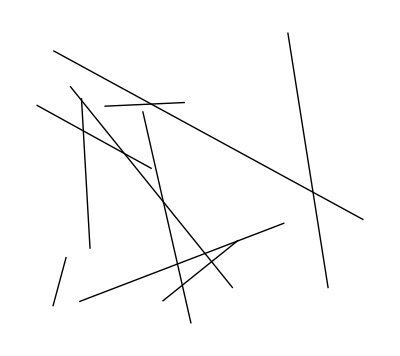

{False,False,True,True,True,False,False,True,False,True}

```mathematica
testLines=Apply[Line@*List,RandomReal[400,{10,2,2}],1];
Graphics[testLines]
Apply[lineIntersectQ,Flatten[lineToPointDelta[#],1]]&/@testLines
```

```mathematica
Gather[testLines,lineIntersectQ[#1,#2]&]
```

{{Line[{{6.22526,5.66303},{4.26962,3.46491}}],Line[{{5.95102,9.48661},{5.43884,2.79496}}],Line[{{5.88395,0.351551},{5.54447,5.79538}}],Line[{{8.95903,5.07541},{4.4909,3.9608}}]},{Line[{{2.77773,4.84041},{7.29648,9.44205}}],Line[{{6.09224,7.07011},{2.15671,9.21048}}],Line[{{2.59699,7.45132},{6.78723,5.67459}}],Line[{{7.33299,8.39259},{2.70055,9.55288}}]},{Line[{{8.0909,8.36123},{4.27937,3.69719}}]},{Line[{{1.06868,0.117816},{1.30631,0.893672}}]}}

```mathematica
showLines[ResourceFunction["PlaceholderImage"][400,400],Gather[testLines,lineIntersectQ[#1,#2]&]]
```

-Graphics-

```mathematica
Flatten[lineToPointDelta[testLines],1]
```

{{6.80893,7.07618},{2.2217,-5.47908},{4.50904,1.65278},{-1.558,2.89003}}

The intersectionQ of each possible pair of lines in the set.

```mathematica
subs=Subsets[#,{2}]&/@testLines;
(*interQ=Apply[lineIntersectQ,#]&/@#&/@subs*)
interQ=Map[Apply[lineIntersectQ],subs,{2}]
```

{{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,True,False},{False,False,True,True,False,False,False,False,False,False,False,True,True,False,False},{},{},{},{},{},{},{}}

```mathematica
Apply[f,#]&/@#&/@subs
```

{{f[Line[{{209.29,130.222},{248.251,131.969}}],Line[{{296.702,134.141},{335.663,135.887}}]],f[Line[{{209.29,130.222},{248.251,131.969}}],Line[{{209.418,139.625},{248.902,138.519}}]],f[Line[{{209.29,130.222},{248.251,131.969}}],Line[{{362.358,135.341},{401.842,134.235}}]],f[Line[{{209.29,130.222},{248.251,131.969}}],Line[{{0.,101.252},{33.9686,118.286}}]],f[Line[{{209.29,130.222},{248.251,131.969}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]],f[Line[{{296.702,134.141},{335.663,135.887}}],Line[{{209.418,139.625},{248.902,138.519}}]],f[Line[{{296.702,134.141},{335.663,135.887}}],Line[{{362.358,135.341},{401.842,134.235}}]],f[Line[{{296.702,134.141},{335.663,135.887}}],Line[{{0.,101.252},{33.9686,118.286}}]],f[Line[{{296.702,134.141},{335.663,135.887}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]],f[Line[{{209.418,139.625},{248.902,138.519}}],Line[{{362.358,135.341},{401.842,134.235}}]],f[Line[{{209.418,139.625},{248.902,138.519}}],Line[{{0.,101.252},{33.9686,118.286}}]],f[Line[{{209.418,139.625},{248.902,138.519}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]],f[Line[{{362.358,135.341},{401.842,134.235}}],Line[{{0.,101.252},{33.9686,118.286}}]],f[Line[{{362.358,135.341},{401.842,134.235}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]],f[Line[{{0.,101.252},{33.9686,118.286}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]]},{f[Line[{{118.095,33.5911},{58.112,0.510363}}],Line[{{108.76,38.6593},{59.4764,10.0211}}]],f[Line[{{118.095,33.5911},{58.112,0.510363}}],Line[{{116.025,101.133},{162.872,126.97}}]],f[Line[{{118.095,33.5911},{58.112,0.510363}}],Line[{{0.,99.5088},{60.9559,134.93}}]],f[Line[{{118.095,33.5911},{58.112,0.510363}}],Line[{{121.541,102.087},{161.356,127.99}}]],f[Line[{{108.76,38.6593},{59.4764,10.0211}}],Line[{{116.025,101.133},{162.872,126.97}}]],f[Line[{{108.76,38.6593},{59.4764,10.0211}}],Line[{{0.,99.5088},{60.9559,134.93}}]],f[Line[{{108.76,38.6593},{59.4764,10.0211}}],Line[{{121.541,102.087},{161.356,127.99}}]],f[Line[{{116.025,101.133},{162.872,126.97}}],Line[{{0.,99.5088},{60.9559,134.93}}]],f[Line[{{116.025,101.133},{162.872,126.97}}],Line[{{121.541,102.087},{161.356,127.99}}]],f[Line[{{0.,99.5088},{60.9559,134.93}}],Line[{{121.541,102.087},{161.356,127.99}}]]},{f[Line[{{0.,34.8693},{61.5843,0.}}],Line[{{58.2313,134.583},{119.527,100.777}}]],f[Line[{{0.,34.8693},{61.5843,0.}}],Line[{{59.033,125.411},{108.586,96.2438}}]],f[Line[{{0.,34.8693},{61.5843,0.}}],Line[{{28.7058,19.8344},{58.4577,0.}}]],f[Line[{{0.,34.8693},{61.5843,0.}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]],f[Line[{{0.,34.8693},{61.5843,0.}}],Line[{{69.7791,120.826},{98.6816,101.087}}]],f[Line[{{58.2313,134.583},{119.527,100.777}}],Line[{{59.033,125.411},{108.586,96.2438}}]],f[Line[{{58.2313,134.583},{119.527,100.777}}],Line[{{28.7058,19.8344},{58.4577,0.}}]],f[Line[{{58.2313,134.583},{119.527,100.777}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]],f[Line[{{58.2313,134.583},{119.527,100.777}}],Line[{{69.7791,120.826},{98.6816,101.087}}]],f[Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{28.7058,19.8344},{58.4577,0.}}]],f[Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]],f[Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{69.7791,120.826},{98.6816,101.087}}]],f[Line[{{28.7058,19.8344},{58.4577,0.}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]],f[Line[{{28.7058,19.8344},{58.4577,0.}}],Line[{{69.7791,120.826},{98.6816,101.087}}]],f[Line[{{23.4969,20.0454},{62.809,1.42271}}],Line[{{69.7791,120.826},{98.6816,101.087}}]]},{},{},{},{},{},{},{}}

```mathematica
Map[Apply[f],subs,{2}]
```

{{f[Line[{{209.29,130.222},{248.251,131.969}}],Line[{{296.702,134.141},{335.663,135.887}}]],f[Line[{{209.29,130.222},{248.251,131.969}}],Line[{{209.418,139.625},{248.902,138.519}}]],f[Line[{{209.29,130.222},{248.251,131.969}}],Line[{{362.358,135.341},{401.842,134.235}}]],f[Line[{{209.29,130.222},{248.251,131.969}}],Line[{{0.,101.252},{33.9686,118.286}}]],f[Line[{{209.29,130.222},{248.251,131.969}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]],f[Line[{{296.702,134.141},{335.663,135.887}}],Line[{{209.418,139.625},{248.902,138.519}}]],f[Line[{{296.702,134.141},{335.663,135.887}}],Line[{{362.358,135.341},{401.842,134.235}}]],f[Line[{{296.702,134.141},{335.663,135.887}}],Line[{{0.,101.252},{33.9686,118.286}}]],f[Line[{{296.702,134.141},{335.663,135.887}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]],f[Line[{{209.418,139.625},{248.902,138.519}}],Line[{{362.358,135.341},{401.842,134.235}}]],f[Line[{{209.418,139.625},{248.902,138.519}}],Line[{{0.,101.252},{33.9686,118.286}}]],f[Line[{{209.418,139.625},{248.902,138.519}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]],f[Line[{{362.358,135.341},{401.842,134.235}}],Line[{{0.,101.252},{33.9686,118.286}}]],f[Line[{{362.358,135.341},{401.842,134.235}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]],f[Line[{{0.,101.252},{33.9686,118.286}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]]},{f[Line[{{118.095,33.5911},{58.112,0.510363}}],Line[{{108.76,38.6593},{59.4764,10.0211}}]],f[Line[{{118.095,33.5911},{58.112,0.510363}}],Line[{{116.025,101.133},{162.872,126.97}}]],f[Line[{{118.095,33.5911},{58.112,0.510363}}],Line[{{0.,99.5088},{60.9559,134.93}}]],f[Line[{{118.095,33.5911},{58.112,0.510363}}],Line[{{121.541,102.087},{161.356,127.99}}]],f[Line[{{108.76,38.6593},{59.4764,10.0211}}],Line[{{116.025,101.133},{162.872,126.97}}]],f[Line[{{108.76,38.6593},{59.4764,10.0211}}],Line[{{0.,99.5088},{60.9559,134.93}}]],f[Line[{{108.76,38.6593},{59.4764,10.0211}}],Line[{{121.541,102.087},{161.356,127.99}}]],f[Line[{{116.025,101.133},{162.872,126.97}}],Line[{{0.,99.5088},{60.9559,134.93}}]],f[Line[{{116.025,101.133},{162.872,126.97}}],Line[{{121.541,102.087},{161.356,127.99}}]],f[Line[{{0.,99.5088},{60.9559,134.93}}],Line[{{121.541,102.087},{161.356,127.99}}]]},{f[Line[{{0.,34.8693},{61.5843,0.}}],Line[{{58.2313,134.583},{119.527,100.777}}]],f[Line[{{0.,34.8693},{61.5843,0.}}],Line[{{59.033,125.411},{108.586,96.2438}}]],f[Line[{{0.,34.8693},{61.5843,0.}}],Line[{{28.7058,19.8344},{58.4577,0.}}]],f[Line[{{0.,34.8693},{61.5843,0.}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]],f[Line[{{0.,34.8693},{61.5843,0.}}],Line[{{69.7791,120.826},{98.6816,101.087}}]],f[Line[{{58.2313,134.583},{119.527,100.777}}],Line[{{59.033,125.411},{108.586,96.2438}}]],f[Line[{{58.2313,134.583},{119.527,100.777}}],Line[{{28.7058,19.8344},{58.4577,0.}}]],f[Line[{{58.2313,134.583},{119.527,100.777}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]],f[Line[{{58.2313,134.583},{119.527,100.777}}],Line[{{69.7791,120.826},{98.6816,101.087}}]],f[Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{28.7058,19.8344},{58.4577,0.}}]],f[Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]],f[Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{69.7791,120.826},{98.6816,101.087}}]],f[Line[{{28.7058,19.8344},{58.4577,0.}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]],f[Line[{{28.7058,19.8344},{58.4577,0.}}],Line[{{69.7791,120.826},{98.6816,101.087}}]],f[Line[{{23.4969,20.0454},{62.809,1.42271}}],Line[{{69.7791,120.826},{98.6816,101.087}}]]},{},{},{},{},{},{},{}}

Get the pairs that intersect, for each set of parallel lines.

```mathematica
subs[[1]]
```

{{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{296.702,134.141},{335.663,135.887}}]},{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{209.418,139.625},{248.902,138.519}}]},{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{362.358,135.341},{401.842,134.235}}]},{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{0.,101.252},{33.9686,118.286}}]},{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]},{Line[{{296.702,134.141},{335.663,135.887}}],Line[{{209.418,139.625},{248.902,138.519}}]},{Line[{{296.702,134.141},{335.663,135.887}}],Line[{{362.358,135.341},{401.842,134.235}}]},{Line[{{296.702,134.141},{335.663,135.887}}],Line[{{0.,101.252},{33.9686,118.286}}]},{Line[{{296.702,134.141},{335.663,135.887}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]},{Line[{{209.418,139.625},{248.902,138.519}}],Line[{{362.358,135.341},{401.842,134.235}}]},{Line[{{209.418,139.625},{248.902,138.519}}],Line[{{0.,101.252},{33.9686,118.286}}]},{Line[{{209.418,139.625},{248.902,138.519}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]},{Line[{{362.358,135.341},{401.842,134.235}}],Line[{{0.,101.252},{33.9686,118.286}}]},{Line[{{362.358,135.341},{401.842,134.235}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]},{Line[{{0.,101.252},{33.9686,118.286}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]}}

```mathematica
{subs[[1]],interQ[[1]]}//Transpose
```

{{{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{296.702,134.141},{335.663,135.887}}]},False},{{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{209.418,139.625},{248.902,138.519}}]},False},{{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{362.358,135.341},{401.842,134.235}}]},False},{{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{0.,101.252},{33.9686,118.286}}]},False},{{Line[{{209.29,130.222},{248.251,131.969}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]},False},{{Line[{{296.702,134.141},{335.663,135.887}}],Line[{{209.418,139.625},{248.902,138.519}}]},False},{{Line[{{296.702,134.141},{335.663,135.887}}],Line[{{362.358,135.341},{401.842,134.235}}]},False},{{Line[{{296.702,134.141},{335.663,135.887}}],Line[{{0.,101.252},{33.9686,118.286}}]},False},{{Line[{{296.702,134.141},{335.663,135.887}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]},False},{{Line[{{209.418,139.625},{248.902,138.519}}],Line[{{362.358,135.341},{401.842,134.235}}]},False},{{Line[{{209.418,139.625},{248.902,138.519}}],Line[{{0.,101.252},{33.9686,118.286}}]},False},{{Line[{{209.418,139.625},{248.902,138.519}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]},False},{{Line[{{362.358,135.341},{401.842,134.235}}],Line[{{0.,101.252},{33.9686,118.286}}]},False},{{Line[{{362.358,135.341},{401.842,134.235}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]},False},{{Line[{{0.,101.252},{33.9686,118.286}}],Line[{{90.9905,17.5126},{56.6488,1.24447}}]},False}}

```mathematica
Transpose[{subs[[3]],interQ[[3]]}]
```

{{{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{58.2313,134.583},{119.527,100.777}}]},False},{{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{59.033,125.411},{108.586,96.2438}}]},False},{{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{28.7058,19.8344},{58.4577,0.}}]},True},{{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]},True},{{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{69.7791,120.826},{98.6816,101.087}}]},False},{{Line[{{58.2313,134.583},{119.527,100.777}}],Line[{{59.033,125.411},{108.586,96.2438}}]},False},{{Line[{{58.2313,134.583},{119.527,100.777}}],Line[{{28.7058,19.8344},{58.4577,0.}}]},False},{{Line[{{58.2313,134.583},{119.527,100.777}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]},False},{{Line[{{58.2313,134.583},{119.527,100.777}}],Line[{{69.7791,120.826},{98.6816,101.087}}]},False},{{Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{28.7058,19.8344},{58.4577,0.}}]},False},{{Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]},False},{{Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{69.7791,120.826},{98.6816,101.087}}]},True},{{Line[{{28.7058,19.8344},{58.4577,0.}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]},True},{{Line[{{28.7058,19.8344},{58.4577,0.}}],Line[{{69.7791,120.826},{98.6816,101.087}}]},False},{{Line[{{23.4969,20.0454},{62.809,1.42271}}],Line[{{69.7791,120.826},{98.6816,101.087}}]},False}}

TODO HERE6

```mathematica
intersections=Select[Transpose[{subs[[3]],interQ[[3]]}],#[[2]]&];
Transpose[intersections]
```

{{{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{28.7058,19.8344},{58.4577,0.}}]},{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]},{Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{69.7791,120.826},{98.6816,101.087}}]},{Line[{{28.7058,19.8344},{58.4577,0.}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]}},{True,True,True,True}}

```mathematica
showLines[images[[10]],%[[1]]]
```

-Graphics-

```mathematica
intersections
```

{{{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{28.7058,19.8344},{58.4577,0.}}]},True},{{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]},True},{{Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{69.7791,120.826},{98.6816,101.087}}]},True},{{Line[{{28.7058,19.8344},{58.4577,0.}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]},True}}

```mathematica
showLines[images[[10]],%]
```

-Graphics-

Some sort of transitive property needed on the lines

```mathematica
testIntersectGrouping={{{Line[{{0.,34.869276548990996},{61.58428950685804,0.}}],Line[{{28.70581129245116,19.834431656498804},{58.457715243255265,0.}}]},True},{{Line[{{0.,34.869276548990996},{61.58428950685804,0.}}],Line[{{23.49690841393103,20.04544124635278},{62.80904364493102,1.4227125639182745}}]},True},{{Line[{{0.,34.869276548990996},{61.58428950685804,0.}}],Line[{{15,15},{50,80}}]},True},{{Line[{{59.0329513311381,125.41107752465874},{108.58615865289636,96.24380744110714}}],Line[{{69.77907374549599,120.82646399454413},{98.68164866966593,101.08713364235783}}]},True},{{Line[{{28.70581129245116,19.834431656498804},{58.457715243255265,0.}}],Line[{{23.49690841393103,20.04544124635278},{62.80904364493102,1.4227125639182745}}]},True}};
```

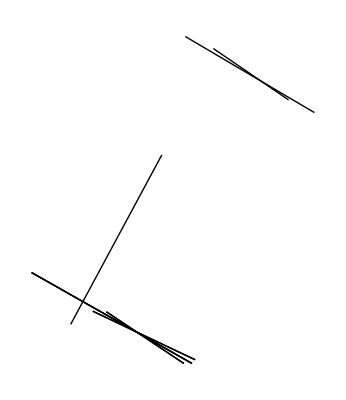

```mathematica
Graphics[testIntersectGrouping[[All,1]]]
```

Here is a way to make sure the lines in each intersection are sorted.

```mathematica
SortBy[{Line[{{28.70581129245116,19.834431656498804},{58.457715243255265,0.}}],Line[{{0.,34.869276548990996},{61.58428950685804,0.}}]},First[#]&]
```

{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{28.7058,19.8344},{58.4577,0.}}]}

```mathematica
testIntersect=Transpose[testIntersectGrouping][[1]]
```

{{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{28.7058,19.8344},{58.4577,0.}}]},{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]},{Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{69.7791,120.826},{98.6816,101.087}}]},{Line[{{28.7058,19.8344},{58.4577,0.}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]}}

```mathematica
testIntersectGroupingSort=SortBy[#,First[#]&]&/@testIntersect
```

{{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{28.7058,19.8344},{58.4577,0.}}]},{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]},{Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{69.7791,120.826},{98.6816,101.087}}]},{Line[{{23.4969,20.0454},{62.809,1.42271}}],Line[{{28.7058,19.8344},{58.4577,0.}}]}}

Can I now take those lines and find commonalities?

1. Gather by common first line in list

```mathematica
First@testIntersectGroupingSort[[1]]
```

Line[{{0.,34.8693},{61.5843,0.}}]

```mathematica
Gather[testIntersectGroupingSort,First[#1]==First[#2]&]
```

{{{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{28.7058,19.8344},{58.4577,0.}}]},{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]}},{{Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{69.7791,120.826},{98.6816,101.087}}]}},{{Line[{{23.4969,20.0454},{62.809,1.42271}}],Line[{{28.7058,19.8344},{58.4577,0.}}]}}}

...so we found that the first two pairs share a line

```mathematica
Merge[]
```

2. Gather by common second line in pair

```mathematica
Gather
```

3. Combine

1. Or gather by sharing an element generally

```mathematica
Part[testIntersectGroupingSort[[1]]][[1]]
```

Line[{{0.,34.8693},{61.5843,0.}}]

```mathematica
Gather[testIntersectGroupingSort,Part[#1][[1]]==Part[#2][[1]]&] (*et cetera*)
```

{{{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{28.7058,19.8344},{58.4577,0.}}]},{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]}},{{Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{69.7791,120.826},{98.6816,101.087}}]}},{{Line[{{23.4969,20.0454},{62.809,1.42271}}],Line[{{28.7058,19.8344},{58.4577,0.}}]}}}

```mathematica
{Part[testIntersectGroupingSort[[1]]],Part[testIntersectGroupingSort][[2]]}
```

{{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{28.7058,19.8344},{58.4577,0.}}]},{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]}}

```mathematica
IntersectingQ@@{Part[testIntersectGroupingSort[[1]]],Part[testIntersectGroupingSort][[2]]}
```

True

I think I’ll have the same problem as before?

```mathematica
finalGroup=Gather[testIntersectGroupingSort,IntersectingQ[Part[#1],Part[#2]]&]
```

{{{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{28.7058,19.8344},{58.4577,0.}}]},{Line[{{0.,34.8693},{61.5843,0.}}],Line[{{23.4969,20.0454},{62.809,1.42271}}]},{Line[{{23.4969,20.0454},{62.809,1.42271}}],Line[{{28.7058,19.8344},{58.4577,0.}}]}},{{Line[{{59.033,125.411},{108.586,96.2438}}],Line[{{69.7791,120.826},{98.6816,101.087}}]}}}

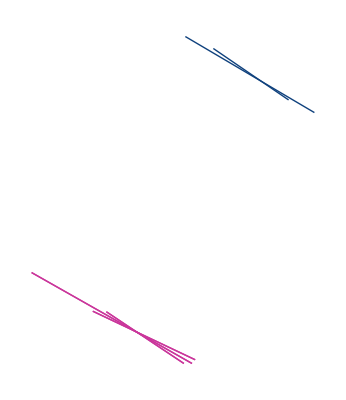

```mathematica
Graphics[{RandomColor[],#}&/@finalGroup]
```

```mathematica
Gather[{{c,d},{c,r},{r,x}},IntersectingQ[#1,#2]&]
```

{{{c,d},{c,r}},{{r,x}}}

```mathematica
Part[f[c,d]]
```

f[c,d]

Try on more examples.

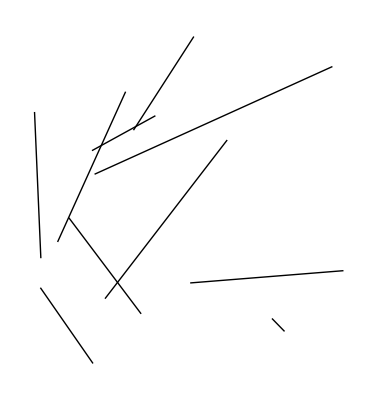

{False,False,True,False,False,False,True,False,True,False}

```mathematica
testLines=Apply[Line@*List,RandomReal[400,{10,2,2}],1];
Graphics[testLines]
Apply[lineIntersectQ,Flatten[lineToPointDelta[#],1]]&/@testLines
```

```mathematica
showLines[ResourceFunction["PlaceholderImage"][400,400],Gather[testLines,lineIntersectQ[#1,#2]&]]
```

```mathematica
Gather[tti,IntersectingQ[Flatten[#1],Flatten[#2]]&]
```

#### Building up Group By Intersecting

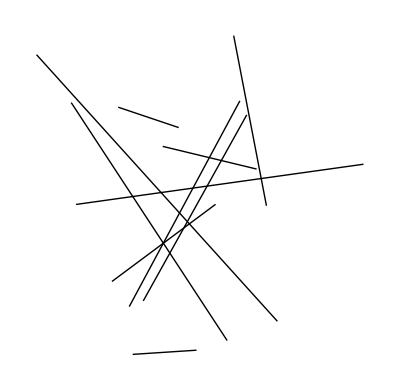

```mathematica
step1=Table[Apply[Line@*List,RandomReal[400,{10,2,2}],1],1];
Graphics[step1]
```

```mathematica
step2=Subsets[#,{2}]&/@step1;
```

```mathematica
step3=Map[Apply[lineIntersectQ],step2,{2}];
```

```mathematica
step4=Partition[Riffle[step2,step3],2];
```

```mathematica
step5=Transpose[#]&/@step4;
```

```mathematica
step6=Select[#,#[[2]]&]&/@step5;
```

```mathematica
step7=Transpose[#][[1]]&/@step6;
```

```mathematica
step8=Gather[#,IntersectingQ[Part[#1],Part[#2]]&]&/@step7;
```

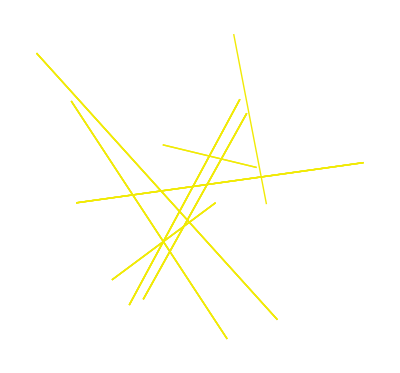

```mathematica
Graphics[{RandomColor[],#}&/@step8]
```

Optional last step tries to see between the sets of lines

```mathematica
step9=Gather[#,IntersectingQ[Flatten[#1],Flatten[#2]]&]&/@step8;
```

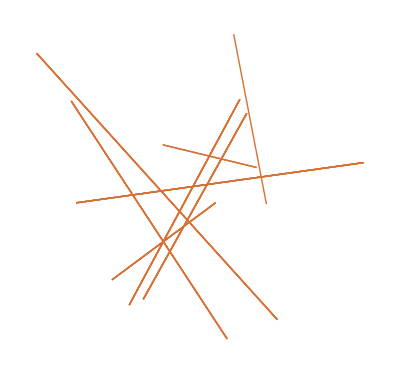

```mathematica
Graphics[{RandomColor[],#}&/@step9]
```

Try out the new function gatherIntersectingLines

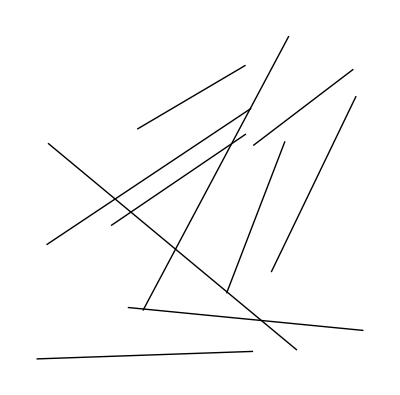

```mathematica
step1=Table[Apply[Line@*List,RandomReal[400,{10,2,2}],1],1];
Graphics[step1]
```

```mathematica
step1
```

{{Line[{{386.352,44.3399},{125.883,69.7156}}],Line[{{262.289,289.998},{36.0578,139.103}}],Line[{{235.015,85.4058},{299.612,253.508}}],Line[{{142.562,66.3013},{303.882,369.821}}],Line[{{37.6929,251.334},{312.831,22.6476}}],Line[{{264.368,21.1615},{25.0197,12.8471}}],Line[{{284.415,108.845},{378.244,303.457}}],Line[{{256.082,337.566},{136.279,266.931}}],Line[{{107.373,160.289},{256.477,261.545}}],Line[{{264.443,248.795},{375.2,333.165}}]}}

```mathematica
Graphics[step1]
```

-Graphics-

```mathematica
gatherIntersectingLines[step1[[1]]]
```

{{{{Line[{{386.352,44.3399},{125.883,69.7156}}],Line[{{142.562,66.3013},{303.882,369.821}}]},{Line[{{386.352,44.3399},{125.883,69.7156}}],Line[{{37.6929,251.334},{312.831,22.6476}}]},{Line[{{262.289,289.998},{36.0578,139.103}}],Line[{{142.562,66.3013},{303.882,369.821}}]},{Line[{{142.562,66.3013},{303.882,369.821}}],Line[{{37.6929,251.334},{312.831,22.6476}}]},{Line[{{142.562,66.3013},{303.882,369.821}}],Line[{{107.373,160.289},{256.477,261.545}}]}},{{Line[{{262.289,289.998},{36.0578,139.103}}],Line[{{37.6929,251.334},{312.831,22.6476}}]},{Line[{{235.015,85.4058},{299.612,253.508}}],Line[{{37.6929,251.334},{312.831,22.6476}}]},{Line[{{37.6929,251.334},{312.831,22.6476}}],Line[{{107.373,160.289},{256.477,261.545}}]}}}}

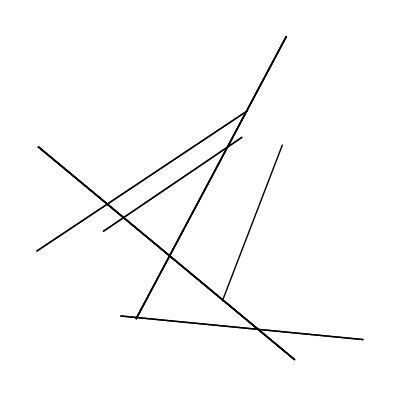

```mathematica
Graphics[%]
```

#### Highligh intersections of parallel lines on the image

```mathematica
With[{i=images[[11]],t=0.07,d=0.02},
lines=ImageLines[ColorNegate@i,Method->{"Segmented"->True}];
longLines=Select[Flatten@flattenLines@lines,lineDistance[#]>25.&];
HighlightImage[i,{RandomColor[],#}&/@longLines]
]
```

-Graphics-

```mathematica
longLines
```

{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{156.339,41.5112},{203.455,13.1371}}],Line[{{78.9632,39.0766},{148.431,36.9545}}],Line[{{124.325,130.495},{167.706,101.823}}],Line[{{270.318,34.0009},{306.607,10.0151}}],Line[{{167.418,101.733},{145.704,36.766}}],Line[{{261.271,36.9254},{321.383,4.08122}}],Line[{{377.02,37.8759},{436.797,3.41394}}],Line[{{609.523,37.8637},{548.353,3.83225}}],Line[{{378.702,37.7517},{317.532,3.72027}}],Line[{{491.057,37.9948},{552.228,3.96335}}],Line[{{57.6093,104.228},{80.6292,37.0634}}],Line[{{607.124,37.7029},{668.164,3.43819}}],Line[{{492.562,37.9424},{434.176,3.08436}}],Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{724.,36.9775},{665.651,3.04175}}],Line[{{126.205,131.757},{170.432,97.4056}}],Line[{{164.287,96.0256},{213.661,123.494}}],Line[{{84.9498,36.9294},{147.913,39.0934}}],Line[{{10.3484,131.064},{41.3937,110.029}}],Line[{{58.1613,99.9657},{100.388,131.996}}],Line[{{206.59,130.057},{163.304,102.154}}],Line[{{475.605,26.0993},{432.27,4.32028}}],Line[{{705.683,25.2113},{663.688,4.10581}}],Line[{{396.785,27.9005},{432.475,3.91727}}],Line[{{396.225,25.0836},{438.38,4.2994}}],Line[{{164.182,96.8266},{152.882,53.2687}}],Line[{{613.351,36.0531},{658.318,7.06635}}],Line[{{171.887,21.5891},{209.64,2.07078}}],Line[{{65.2987,106.733},{95.6311,126.123}}],Line[{{165.918,92.281},{150.049,53.3943}}],Line[{{605.489,37.0351},{563.464,9.94472}}],Line[{{502.67,32.9148},{542.495,7.02668}}],Line[{{374.273,36.8658},{332.668,10.0463}}],Line[{{164.447,96.9882},{198.782,113.27}}],Line[{{22.177,121.098},{52.9533,106.647}}],Line[{{631.386,22.9956},{669.576,4.34702}}],Line[{{722.336,37.6512},{691.547,17.1318}}],Line[{{516.396,22.1731},{553.893,4.39158}}],Line[{{63.9105,90.7216},{75.185,49.226}}],Line[{{72.1849,109.044},{92.9712,127.049}}]}

```mathematica
step2=gatherParallelLines[longLines,0.8]
```

{{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{156.339,41.5112},{203.455,13.1371}}],Line[{{78.9632,39.0766},{148.431,36.9545}}],Line[{{124.325,130.495},{167.706,101.823}}],Line[{{270.318,34.0009},{306.607,10.0151}}],Line[{{261.271,36.9254},{321.383,4.08122}}],Line[{{377.02,37.8759},{436.797,3.41394}}],Line[{{491.057,37.9948},{552.228,3.96335}}],Line[{{607.124,37.7029},{668.164,3.43819}}],Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{126.205,131.757},{170.432,97.4056}}],Line[{{84.9498,36.9294},{147.913,39.0934}}],Line[{{10.3484,131.064},{41.3937,110.029}}],Line[{{396.785,27.9005},{432.475,3.91727}}],Line[{{396.225,25.0836},{438.38,4.2994}}],Line[{{613.351,36.0531},{658.318,7.06635}}],Line[{{171.887,21.5891},{209.64,2.07078}}],Line[{{502.67,32.9148},{542.495,7.02668}}],Line[{{22.177,121.098},{52.9533,106.647}}],Line[{{631.386,22.9956},{669.576,4.34702}}],Line[{{516.396,22.1731},{553.893,4.39158}}]},{Line[{{167.418,101.733},{145.704,36.766}}],Line[{{165.918,92.281},{150.049,53.3943}}]},{Line[{{609.523,37.8637},{548.353,3.83225}}],Line[{{378.702,37.7517},{317.532,3.72027}}],Line[{{492.562,37.9424},{434.176,3.08436}}],Line[{{724.,36.9775},{665.651,3.04175}}],Line[{{164.287,96.0256},{213.661,123.494}}],Line[{{58.1613,99.9657},{100.388,131.996}}],Line[{{206.59,130.057},{163.304,102.154}}],Line[{{475.605,26.0993},{432.27,4.32028}}],Line[{{705.683,25.2113},{663.688,4.10581}}],Line[{{65.2987,106.733},{95.6311,126.123}}],Line[{{605.489,37.0351},{563.464,9.94472}}],Line[{{374.273,36.8658},{332.668,10.0463}}],Line[{{164.447,96.9882},{198.782,113.27}}],Line[{{722.336,37.6512},{691.547,17.1318}}],Line[{{72.1849,109.044},{92.9712,127.049}}]},{Line[{{57.6093,104.228},{80.6292,37.0634}}],Line[{{63.9105,90.7216},{75.185,49.226}}]},{Line[{{164.182,96.8266},{152.882,53.2687}}]}}

```mathematica
showLines[images[[11]],step2]
```

-Graphics-

Debug resulting in simplifying the function.

Fix for sets with just one line - it’s already a merged group, so don’t remove it.

```mathematica
s1=step2[[1]]
```

{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{156.339,41.5112},{203.455,13.1371}}],Line[{{78.9632,39.0766},{148.431,36.9545}}],Line[{{124.325,130.495},{167.706,101.823}}],Line[{{270.318,34.0009},{306.607,10.0151}}],Line[{{261.271,36.9254},{321.383,4.08122}}],Line[{{377.02,37.8759},{436.797,3.41394}}],Line[{{491.057,37.9948},{552.228,3.96335}}],Line[{{607.124,37.7029},{668.164,3.43819}}],Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{126.205,131.757},{170.432,97.4056}}],Line[{{84.9498,36.9294},{147.913,39.0934}}],Line[{{10.3484,131.064},{41.3937,110.029}}],Line[{{396.785,27.9005},{432.475,3.91727}}],Line[{{396.225,25.0836},{438.38,4.2994}}],Line[{{613.351,36.0531},{658.318,7.06635}}],Line[{{171.887,21.5891},{209.64,2.07078}}],Line[{{502.67,32.9148},{542.495,7.02668}}],Line[{{22.177,121.098},{52.9533,106.647}}],Line[{{631.386,22.9956},{669.576,4.34702}}],Line[{{516.396,22.1731},{553.893,4.39158}}]}

```mathematica
gatherIntersectingLines[s1]
```

{{{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{1.32178,133.75},{61.6832,101.366}}]},{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{10.3484,131.064},{41.3937,110.029}}]},{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{22.177,121.098},{52.9533,106.647}}]},{Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{10.3484,131.064},{41.3937,110.029}}]},{Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{22.177,121.098},{52.9533,106.647}}]}},{{Line[{{78.9632,39.0766},{148.431,36.9545}}],Line[{{84.9498,36.9294},{147.913,39.0934}}]}},{{Line[{{124.325,130.495},{167.706,101.823}}],Line[{{126.205,131.757},{170.432,97.4056}}]}},{{Line[{{270.318,34.0009},{306.607,10.0151}}],Line[{{261.271,36.9254},{321.383,4.08122}}]}},{{Line[{{377.02,37.8759},{436.797,3.41394}}],Line[{{396.785,27.9005},{432.475,3.91727}}]},{Line[{{377.02,37.8759},{436.797,3.41394}}],Line[{{396.225,25.0836},{438.38,4.2994}}]},{Line[{{396.785,27.9005},{432.475,3.91727}}],Line[{{396.225,25.0836},{438.38,4.2994}}]}},{{Line[{{491.057,37.9948},{552.228,3.96335}}],Line[{{502.67,32.9148},{542.495,7.02668}}]},{Line[{{491.057,37.9948},{552.228,3.96335}}],Line[{{516.396,22.1731},{553.893,4.39158}}]},{Line[{{502.67,32.9148},{542.495,7.02668}}],Line[{{516.396,22.1731},{553.893,4.39158}}]}},{{Line[{{607.124,37.7029},{668.164,3.43819}}],Line[{{613.351,36.0531},{658.318,7.06635}}]},{Line[{{607.124,37.7029},{668.164,3.43819}}],Line[{{631.386,22.9956},{669.576,4.34702}}]},{Line[{{613.351,36.0531},{658.318,7.06635}}],Line[{{631.386,22.9956},{669.576,4.34702}}]}},{{Line[{{10.3484,131.064},{41.3937,110.029}}],Line[{{22.177,121.098},{52.9533,106.647}}]}}}

```mathematica
s2=Subsets[s1,{2}]
```

{}

Solution: if length<2,  do not look for intersections.

```mathematica
s2=If[
Length[s1]<2
,{s1}
,Subsets[s1,{2}]]
```

{{Line[{{164.182,96.8266},{152.882,53.2687}}]}}

Should I define it so lineIntersectQ returns False if given only one line? Instead, I just made gatherIntersectingLines return the list containing a single line enclosed in an extra list.

```mathematica
Apply[lineIntersectQ,s2,{1}]
```

{lineIntersectQ[Line[{{164.182,96.8266},{152.882,53.2687}}]]}

Old debugging

```mathematica
s1=step2[[1]];
s2=Subsets[s1,{2}];
```

```mathematica
s3=Apply[lineIntersectQ,s2,{1}];
(*s4=Partition[Riffle[s2,s3],2];*)
s4=Transpose[{s2,s3}];
s5=s4;
```

```mathematica
s6=Select[s5,#[[2]]&];
```

```mathematica
s7=Transpose[s6][[1]];
```

```mathematica
s8=Gather[s7,IntersectingQ[Part[#1],Part[#2]]&];
```

{{{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{1.32178,133.75},{61.6832,101.366}}]},{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{10.3484,131.064},{41.3937,110.029}}]},{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{22.177,121.098},{52.9533,106.647}}]},{Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{10.3484,131.064},{41.3937,110.029}}]},{Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{22.177,121.098},{52.9533,106.647}}]}},{{Line[{{78.9632,39.0766},{148.431,36.9545}}],Line[{{84.9498,36.9294},{147.913,39.0934}}]}},{{Line[{{124.325,130.495},{167.706,101.823}}],Line[{{126.205,131.757},{170.432,97.4056}}]}},{{Line[{{270.318,34.0009},{306.607,10.0151}}],Line[{{261.271,36.9254},{321.383,4.08122}}]}},{{Line[{{377.02,37.8759},{436.797,3.41394}}],Line[{{396.785,27.9005},{432.475,3.91727}}]},{Line[{{377.02,37.8759},{436.797,3.41394}}],Line[{{396.225,25.0836},{438.38,4.2994}}]},{Line[{{396.785,27.9005},{432.475,3.91727}}],Line[{{396.225,25.0836},{438.38,4.2994}}]}},{{Line[{{491.057,37.9948},{552.228,3.96335}}],Line[{{502.67,32.9148},{542.495,7.02668}}]},{Line[{{491.057,37.9948},{552.228,3.96335}}],Line[{{516.396,22.1731},{553.893,4.39158}}]},{Line[{{502.67,32.9148},{542.495,7.02668}}],Line[{{516.396,22.1731},{553.893,4.39158}}]}},{{Line[{{607.124,37.7029},{668.164,3.43819}}],Line[{{613.351,36.0531},{658.318,7.06635}}]},{Line[{{607.124,37.7029},{668.164,3.43819}}],Line[{{631.386,22.9956},{669.576,4.34702}}]},{Line[{{613.351,36.0531},{658.318,7.06635}}],Line[{{631.386,22.9956},{669.576,4.34702}}]}},{{Line[{{10.3484,131.064},{41.3937,110.029}}],Line[{{22.177,121.098},{52.9533,106.647}}]}}}

```mathematica
gatherIntersectingLines[step2[[1;;2]]]
```

gatherIntersectingLines[{{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{156.339,41.5112},{203.455,13.1371}}],Line[{{78.9632,39.0766},{148.431,36.9545}}],Line[{{124.325,130.495},{167.706,101.823}}],Line[{{270.318,34.0009},{306.607,10.0151}}],Line[{{261.271,36.9254},{321.383,4.08122}}],Line[{{377.02,37.8759},{436.797,3.41394}}],Line[{{491.057,37.9948},{552.228,3.96335}}],Line[{{607.124,37.7029},{668.164,3.43819}}],Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{126.205,131.757},{170.432,97.4056}}],Line[{{84.9498,36.9294},{147.913,39.0934}}],Line[{{10.3484,131.064},{41.3937,110.029}}],Line[{{396.785,27.9005},{432.475,3.91727}}],Line[{{396.225,25.0836},{438.38,4.2994}}],Line[{{613.351,36.0531},{658.318,7.06635}}],Line[{{171.887,21.5891},{209.64,2.07078}}],Line[{{502.67,32.9148},{542.495,7.02668}}],Line[{{22.177,121.098},{52.9533,106.647}}],Line[{{631.386,22.9956},{669.576,4.34702}}],Line[{{516.396,22.1731},{553.893,4.39158}}]},{Line[{{167.418,101.733},{145.704,36.766}}],Line[{{165.918,92.281},{150.049,53.3943}}]}}]

```mathematica
step2
```

{{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{156.339,41.5112},{203.455,13.1371}}],Line[{{78.9632,39.0766},{148.431,36.9545}}],Line[{{124.325,130.495},{167.706,101.823}}],Line[{{270.318,34.0009},{306.607,10.0151}}],Line[{{261.271,36.9254},{321.383,4.08122}}],Line[{{377.02,37.8759},{436.797,3.41394}}],Line[{{491.057,37.9948},{552.228,3.96335}}],Line[{{607.124,37.7029},{668.164,3.43819}}],Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{126.205,131.757},{170.432,97.4056}}],Line[{{84.9498,36.9294},{147.913,39.0934}}],Line[{{10.3484,131.064},{41.3937,110.029}}],Line[{{396.785,27.9005},{432.475,3.91727}}],Line[{{396.225,25.0836},{438.38,4.2994}}],Line[{{613.351,36.0531},{658.318,7.06635}}],Line[{{171.887,21.5891},{209.64,2.07078}}],Line[{{502.67,32.9148},{542.495,7.02668}}],Line[{{22.177,121.098},{52.9533,106.647}}],Line[{{631.386,22.9956},{669.576,4.34702}}],Line[{{516.396,22.1731},{553.893,4.39158}}]},{Line[{{167.418,101.733},{145.704,36.766}}],Line[{{165.918,92.281},{150.049,53.3943}}]},{Line[{{609.523,37.8637},{548.353,3.83225}}],Line[{{378.702,37.7517},{317.532,3.72027}}],Line[{{492.562,37.9424},{434.176,3.08436}}],Line[{{724.,36.9775},{665.651,3.04175}}],Line[{{164.287,96.0256},{213.661,123.494}}],Line[{{58.1613,99.9657},{100.388,131.996}}],Line[{{206.59,130.057},{163.304,102.154}}],Line[{{475.605,26.0993},{432.27,4.32028}}],Line[{{705.683,25.2113},{663.688,4.10581}}],Line[{{65.2987,106.733},{95.6311,126.123}}],Line[{{605.489,37.0351},{563.464,9.94472}}],Line[{{374.273,36.8658},{332.668,10.0463}}],Line[{{164.447,96.9882},{198.782,113.27}}],Line[{{722.336,37.6512},{691.547,17.1318}}],Line[{{72.1849,109.044},{92.9712,127.049}}]},{Line[{{57.6093,104.228},{80.6292,37.0634}}],Line[{{63.9105,90.7216},{75.185,49.226}}]},{Line[{{164.182,96.8266},{152.882,53.2687}}]}}

```mathematica
showLines[images[[11]],step4[[1]]]
```

-Graphics-

```mathematica
step3=gatherIntersectingLines/@step2
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

{{{{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{1.32178,133.75},{61.6832,101.366}}]},{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{10.3484,131.064},{41.3937,110.029}}]},{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{22.177,121.098},{52.9533,106.647}}]},{Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{10.3484,131.064},{41.3937,110.029}}]},{Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{22.177,121.098},{52.9533,106.647}}]}},{{Line[{{78.9632,39.0766},{148.431,36.9545}}],Line[{{84.9498,36.9294},{147.913,39.0934}}]}},{{Line[{{124.325,130.495},{167.706,101.823}}],Line[{{126.205,131.757},{170.432,97.4056}}]}},{{Line[{{270.318,34.0009},{306.607,10.0151}}],Line[{{261.271,36.9254},{321.383,4.08122}}]}},{{Line[{{377.02,37.8759},{436.797,3.41394}}],Line[{{396.785,27.9005},{432.475,3.91727}}]},{Line[{{377.02,37.8759},{436.797,3.41394}}],Line[{{396.225,25.0836},{438.38,4.2994}}]},{Line[{{396.785,27.9005},{432.475,3.91727}}],Line[{{396.225,25.0836},{438.38,4.2994}}]}},{{Line[{{491.057,37.9948},{552.228,3.96335}}],Line[{{502.67,32.9148},{542.495,7.02668}}]},{Line[{{491.057,37.9948},{552.228,3.96335}}],Line[{{516.396,22.1731},{553.893,4.39158}}]},{Line[{{502.67,32.9148},{542.495,7.02668}}],Line[{{516.396,22.1731},{553.893,4.39158}}]}},{{Line[{{607.124,37.7029},{668.164,3.43819}}],Line[{{613.351,36.0531},{658.318,7.06635}}]},{Line[{{607.124,37.7029},{668.164,3.43819}}],Line[{{631.386,22.9956},{669.576,4.34702}}]},{Line[{{613.351,36.0531},{658.318,7.06635}}],Line[{{631.386,22.9956},{669.576,4.34702}}]}},{{Line[{{10.3484,131.064},{41.3937,110.029}}],Line[{{22.177,121.098},{52.9533,106.647}}]}}},{{{Line[{{167.418,101.733},{145.704,36.766}}],Line[{{165.918,92.281},{150.049,53.3943}}]}}},{{{Line[{{609.523,37.8637},{548.353,3.83225}}],Line[{{605.489,37.0351},{563.464,9.94472}}]}},{{Line[{{378.702,37.7517},{317.532,3.72027}}],Line[{{374.273,36.8658},{332.668,10.0463}}]}},{{Line[{{492.562,37.9424},{434.176,3.08436}}],Line[{{475.605,26.0993},{432.27,4.32028}}]}},{{Line[{{724.,36.9775},{665.651,3.04175}}],Line[{{705.683,25.2113},{663.688,4.10581}}]},{Line[{{724.,36.9775},{665.651,3.04175}}],Line[{{722.336,37.6512},{691.547,17.1318}}]},{Line[{{705.683,25.2113},{663.688,4.10581}}],Line[{{722.336,37.6512},{691.547,17.1318}}]}},{{Line[{{164.287,96.0256},{213.661,123.494}}],Line[{{164.447,96.9882},{198.782,113.27}}]}},{{Line[{{58.1613,99.9657},{100.388,131.996}}],Line[{{65.2987,106.733},{95.6311,126.123}}]},{Line[{{58.1613,99.9657},{100.388,131.996}}],Line[{{72.1849,109.044},{92.9712,127.049}}]},{Line[{{65.2987,106.733},{95.6311,126.123}}],Line[{{72.1849,109.044},{92.9712,127.049}}]}}},{{{Line[{{57.6093,104.228},{80.6292,37.0634}}],Line[{{63.9105,90.7216},{75.185,49.226}}]}}},{}}

```mathematica
Map[mergeLines,step4,{2}]
```

{{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{78.9632,39.0766},{148.431,36.9545}}],Line[{{124.325,130.495},{170.432,97.4056}}],Line[{{261.271,36.9254},{321.383,4.08122}}],Line[{{377.02,37.8759},{438.38,4.2994}}],Line[{{491.057,37.9948},{553.893,4.39158}}],Line[{{607.124,37.7029},{669.576,4.34702}}],Line[{{10.3484,131.064},{52.9533,106.647}}]},{Line[{{167.418,101.733},{145.704,36.766}}]},{Line[{{609.523,37.8637},{548.353,3.83225}}],Line[{{378.702,37.7517},{317.532,3.72027}}],Line[{{432.27,4.32028},{492.562,37.9424}}],Line[{{663.688,4.10581},{724.,36.9775}}],Line[{{164.287,96.0256},{213.661,123.494}}],Line[{{58.1613,99.9657},{100.388,131.996}}]},{Line[{{57.6093,104.228},{80.6292,37.0634}}]},{}}

```mathematica
HighlightImage[images[[11]],Map[mergeLines,step4,{2}]]
```

-Graphics-

Note that in the above, Line[{{22.177,121.098},{52.9533,106.647}}] appears twice

```mathematica
step4=Map[Union@*Flatten,step3,{2}]
```

{{{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{10.3484,131.064},{41.3937,110.029}}],Line[{{22.177,121.098},{52.9533,106.647}}]},{Line[{{78.9632,39.0766},{148.431,36.9545}}],Line[{{84.9498,36.9294},{147.913,39.0934}}]},{Line[{{124.325,130.495},{167.706,101.823}}],Line[{{126.205,131.757},{170.432,97.4056}}]},{Line[{{261.271,36.9254},{321.383,4.08122}}],Line[{{270.318,34.0009},{306.607,10.0151}}]},{Line[{{377.02,37.8759},{436.797,3.41394}}],Line[{{396.225,25.0836},{438.38,4.2994}}],Line[{{396.785,27.9005},{432.475,3.91727}}]},{Line[{{491.057,37.9948},{552.228,3.96335}}],Line[{{502.67,32.9148},{542.495,7.02668}}],Line[{{516.396,22.1731},{553.893,4.39158}}]},{Line[{{607.124,37.7029},{668.164,3.43819}}],Line[{{613.351,36.0531},{658.318,7.06635}}],Line[{{631.386,22.9956},{669.576,4.34702}}]},{Line[{{10.3484,131.064},{41.3937,110.029}}],Line[{{22.177,121.098},{52.9533,106.647}}]}},{{Line[{{165.918,92.281},{150.049,53.3943}}],Line[{{167.418,101.733},{145.704,36.766}}]}},{{Line[{{605.489,37.0351},{563.464,9.94472}}],Line[{{609.523,37.8637},{548.353,3.83225}}]},{Line[{{374.273,36.8658},{332.668,10.0463}}],Line[{{378.702,37.7517},{317.532,3.72027}}]},{Line[{{475.605,26.0993},{432.27,4.32028}}],Line[{{492.562,37.9424},{434.176,3.08436}}]},{Line[{{705.683,25.2113},{663.688,4.10581}}],Line[{{722.336,37.6512},{691.547,17.1318}}],Line[{{724.,36.9775},{665.651,3.04175}}]},{Line[{{164.287,96.0256},{213.661,123.494}}],Line[{{164.447,96.9882},{198.782,113.27}}]},{Line[{{58.1613,99.9657},{100.388,131.996}}],Line[{{65.2987,106.733},{95.6311,126.123}}],Line[{{72.1849,109.044},{92.9712,127.049}}]}},{{Line[{{57.6093,104.228},{80.6292,37.0634}}],Line[{{63.9105,90.7216},{75.185,49.226}}]}},{}}

```mathematica
step4/.{Line[{{22.177015355183407,121.09750139938711},{52.953281562376716,106.6468461082257}}]->Red}
```

{{{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{10.3484,131.064},{41.3937,110.029}}],RGBColor[1, 0, 0]},{Line[{{78.9632,39.0766},{148.431,36.9545}}],Line[{{84.9498,36.9294},{147.913,39.0934}}]},{Line[{{124.325,130.495},{167.706,101.823}}],Line[{{126.205,131.757},{170.432,97.4056}}]},{Line[{{261.271,36.9254},{321.383,4.08122}}],Line[{{270.318,34.0009},{306.607,10.0151}}]},{Line[{{377.02,37.8759},{436.797,3.41394}}],Line[{{396.225,25.0836},{438.38,4.2994}}],Line[{{396.785,27.9005},{432.475,3.91727}}]},{Line[{{491.057,37.9948},{552.228,3.96335}}],Line[{{502.67,32.9148},{542.495,7.02668}}],Line[{{516.396,22.1731},{553.893,4.39158}}]},{Line[{{607.124,37.7029},{668.164,3.43819}}],Line[{{613.351,36.0531},{658.318,7.06635}}],Line[{{631.386,22.9956},{669.576,4.34702}}]},{Line[{{10.3484,131.064},{41.3937,110.029}}],RGBColor[1, 0, 0]}},{{Line[{{165.918,92.281},{150.049,53.3943}}],Line[{{167.418,101.733},{145.704,36.766}}]}},{{Line[{{605.489,37.0351},{563.464,9.94472}}],Line[{{609.523,37.8637},{548.353,3.83225}}]},{Line[{{374.273,36.8658},{332.668,10.0463}}],Line[{{378.702,37.7517},{317.532,3.72027}}]},{Line[{{475.605,26.0993},{432.27,4.32028}}],Line[{{492.562,37.9424},{434.176,3.08436}}]},{Line[{{705.683,25.2113},{663.688,4.10581}}],Line[{{722.336,37.6512},{691.547,17.1318}}],Line[{{724.,36.9775},{665.651,3.04175}}]},{Line[{{164.287,96.0256},{213.661,123.494}}],Line[{{164.447,96.9882},{198.782,113.27}}]},{Line[{{58.1613,99.9657},{100.388,131.996}}],Line[{{65.2987,106.733},{95.6311,126.123}}],Line[{{72.1849,109.044},{92.9712,127.049}}]}},{{Line[{{57.6093,104.228},{80.6292,37.0634}}],Line[{{63.9105,90.7216},{75.185,49.226}}]}},{}}

Check for duplicates after the sets of intersecting lines are taken out?

```mathematica
step4
```

```mathematica
{{{Line[{{1.284980285452311,134.88769564532683},{60.82240017807605,99.03318919872503}}],Line[{{1.3217837744715386,133.75022372943477},{61.68324280867179,101.36590247265119}}],Line[{{10.348420309549354,131.06378287289698},{41.393681238197416,110.02948293512493}}],Line[{{22.177015355183407,121.09750139938711},{52.953281562376716,106.6468461082257}}]},{Line[{{78.96316646563781,39.07655336043578},{148.4307622803445,36.95449499070433}}],Line[{{84.94984302827041,36.929415932265954},{147.91266786098848,39.09336812315677}}]},{Line[{{124.32546425054159,130.4954973672686},{167.70608186857925,101.82282719029342}}],Line[{{126.20516552763402,131.75715052156764},{170.43156375727787,97.40564837634909}}]},{Line[{{261.27067193757335,36.925423734745365},{321.3831365067365,4.081221759037277}}],Line[{{270.3179273881683,34.00093427167904},{306.6074825109497,10.015142873632499}}]},{Line[{{377.01954998567203,37.87592018350786},{436.79723991082903,3.4139442214161306}}],Line[{{396.22516040351195,25.083616481928274},{438.3798322731292,4.29940036572836}}],Line[{{396.78479325353965,27.90053832093251},{432.47516893002006,3.9172715694722626}}]},{Line[{{491.0572152948204,37.99476669131138},{552.2279839194357,3.963353763344628}}],Line[{{502.6698250904382,32.914773349674164},{542.4951518783471,7.026680599603338}}],Line[{{516.395581176817,22.17314198663223},{553.8931263995272,4.3915756250653715}}]},{Line[{{607.12407998433,37.70285668568101},{668.1644970127282,3.4381884544076513}}],Line[{{613.351355025532,36.05308134712925},{658.3182262023388,7.066351683911535}}],Line[{{631.3858898555122,22.9956125875419},{669.5759404382582,4.347019169074315}}]},{Line[{{10.348420309549354,131.06378287289698},{41.393681238197416,110.02948293512493}}],Line[{{22.177015355183407,121.09750139938711},{52.953281562376716,106.6468461082257}}]}},{{Line[{{165.91809959720374,92.28103718775418},{150.04928135059617,53.39427070536156}}],Line[{{167.41812826811227,101.73332107208432},{145.7041133546005,36.766009627514066}}]}},{{Line[{{605.4891806368271,37.0351220166492},{563.464067387475,9.944720462240113}}],Line[{{609.5232758596486,37.86366567633318},{548.3525072350333,3.8322527483664004}}]},{Line[{{374.2728020979704,36.86579339376148},{332.6679399811118,10.0462958548965}}],Line[{{378.7022775334792,37.75168517039725},{317.5315089088639,3.720272242430468}}]},{Line[{{475.6054146653287,26.099297523885426},{432.2703880871576,4.320283049644274}}],Line[{{492.56233231065005,37.94241222788932},{434.1764059308051,3.084362931244243}}]},{Line[{{705.6831330958246,25.211251605866977},{663.6883650716176,4.105814898870378}}],Line[{{722.3357364915606,37.651202964469725},{691.5468615854331,17.131817446993146}}],Line[{{724.,36.97753567805955},{665.6509408412381,3.041753746780799}}]},{Line[{{164.28720716325248,96.02558517415173},{213.66075612454907,123.49379703743918}}],Line[{{164.44706579598187,96.98816726768538},{198.78216744569235,113.27008345418034}}]},{Line[{{58.16128216624579,99.96573690029268},{100.38796647872562,131.9955219756592}}],Line[{{65.29873715221888,106.7332164650362},{95.6310537648625,126.1226612459046}}],Line[{{72.18493451207601,109.04432615543985},{92.97117219879947,127.04938996624145}}]}},{{Line[{{57.60930760836405,104.22799945078135},{80.62923812759902,37.06340461920662}}],Line[{{63.91048975008175,90.72159383290494},{75.18497642965472,49.22598020794295}}]}},{}}
```

```mathematica
Gather[#,IntersectingQ[Part[#1],Part[#2]]&]&/@step4
```

{{{{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{10.3484,131.064},{41.3937,110.029}}],Line[{{22.177,121.098},{52.9533,106.647}}]},{Line[{{10.3484,131.064},{41.3937,110.029}}],Line[{{22.177,121.098},{52.9533,106.647}}]}},{{Line[{{78.9632,39.0766},{148.431,36.9545}}],Line[{{84.9498,36.9294},{147.913,39.0934}}]}},{{Line[{{124.325,130.495},{167.706,101.823}}],Line[{{126.205,131.757},{170.432,97.4056}}]}},{{Line[{{261.271,36.9254},{321.383,4.08122}}],Line[{{270.318,34.0009},{306.607,10.0151}}]}},{{Line[{{377.02,37.8759},{436.797,3.41394}}],Line[{{396.225,25.0836},{438.38,4.2994}}],Line[{{396.785,27.9005},{432.475,3.91727}}]}},{{Line[{{491.057,37.9948},{552.228,3.96335}}],Line[{{502.67,32.9148},{542.495,7.02668}}],Line[{{516.396,22.1731},{553.893,4.39158}}]}},{{Line[{{607.124,37.7029},{668.164,3.43819}}],Line[{{613.351,36.0531},{658.318,7.06635}}],Line[{{631.386,22.9956},{669.576,4.34702}}]}}},{{{Line[{{165.918,92.281},{150.049,53.3943}}],Line[{{167.418,101.733},{145.704,36.766}}]}}},{{{Line[{{605.489,37.0351},{563.464,9.94472}}],Line[{{609.523,37.8637},{548.353,3.83225}}]}},{{Line[{{374.273,36.8658},{332.668,10.0463}}],Line[{{378.702,37.7517},{317.532,3.72027}}]}},{{Line[{{475.605,26.0993},{432.27,4.32028}}],Line[{{492.562,37.9424},{434.176,3.08436}}]}},{{Line[{{705.683,25.2113},{663.688,4.10581}}],Line[{{722.336,37.6512},{691.547,17.1318}}],Line[{{724.,36.9775},{665.651,3.04175}}]}},{{Line[{{164.287,96.0256},{213.661,123.494}}],Line[{{164.447,96.9882},{198.782,113.27}}]}},{{Line[{{58.1613,99.9657},{100.388,131.996}}],Line[{{65.2987,106.733},{95.6311,126.123}}],Line[{{72.1849,109.044},{92.9712,127.049}}]}}},{{{Line[{{57.6093,104.228},{80.6292,37.0634}}],Line[{{63.9105,90.7216},{75.185,49.226}}]}}},{}}

```mathematica
step6=Map[,step5,{2}]
```

{{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{78.9632,39.0766},{148.431,36.9545}}],Line[{{124.325,130.495},{170.432,97.4056}}],Line[{{261.271,36.9254},{321.383,4.08122}}],Line[{{377.02,37.8759},{438.38,4.2994}}],Line[{{491.057,37.9948},{553.893,4.39158}}],Line[{{607.124,37.7029},{669.576,4.34702}}],Line[{{10.3484,131.064},{52.9533,106.647}}]},{Line[{{167.418,101.733},{145.704,36.766}}]},{Line[{{609.523,37.8637},{548.353,3.83225}}],Line[{{378.702,37.7517},{317.532,3.72027}}],Line[{{432.27,4.32028},{492.562,37.9424}}],Line[{{663.688,4.10581},{724.,36.9775}}],Line[{{164.287,96.0256},{213.661,123.494}}],Line[{{58.1613,99.9657},{100.388,131.996}}]},{Line[{{57.6093,104.228},{80.6292,37.0634}}]},{}}

```mathematica
HighlightImage[images[[11]],testEnd[[1,2]]]
```

-Graphics-

#### Merge lines

Subsets then map

```mathematica
step4[[1,8]]
```

{Line[{{10.3484,131.064},{41.3937,110.029}}],Line[{{22.177,121.098},{52.9533,106.647}}]}

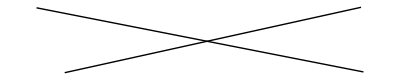

```mathematica
Graphics[step4[[1,2]]]
```

```mathematica
step4[[1,5]]
```

{Line[{{377.02,37.8759},{436.797,3.41394}}],Line[{{396.225,25.0836},{438.38,4.2994}}],Line[{{396.785,27.9005},{432.475,3.91727}}]}

```mathematica
mergeLines[step4[[1,5]]]
```

Line[{{377.02,37.8759},{438.38,4.2994}}]

```mathematica
DownValues[mergeLines]
```

{HoldPattern[mergeLines[ChemicalRead`Private`lines:{Repeated[Line[_?MatrixQ],{2,∞}]}]]:>Block[{ChemicalRead`Private`pts,ChemicalRead`Private`subs,ChemicalRead`Private`bigLine},ChemicalRead`Private`pts=Flatten[First/@ChemicalRead`Private`lines,1];ChemicalRead`Private`subs=Subsets[ChemicalRead`Private`pts,{2}];ChemicalRead`Private`bigLine=MaximalBy[ChemicalRead`Private`subs,Apply[EuclideanDistance]];Return[Line@@ChemicalRead`Private`bigLine];]}

```mathematica
subs=Subsets[pts,{2}];
```

```mathematica
Map[Apply[EuclideanDistance],subs]
```

{69.5,1.13807,69.0772,9.83709,47.1873,25.0329,58.8826,68.8883,2.48648,59.7794,22.3247,44.5006,10.9495,68.5,9.41792,46.5664,24.3933,58.313,59.3062,22.0618,44.1597,10.203,37.5,15.4675,49.1056,22.1761,12.0444,34.}

```mathematica
MaximalBy[subs,Apply[EuclideanDistance]]
```

{{{1.28498,134.888},{60.8224,99.0332}}}

```mathematica
Apply[Line,MaximalBy[subs,Apply[EuclideanDistance]]]
```

Line[{{1.28498,134.888},{60.8224,99.0332}}]

```mathematica
mergeLines[step4[[1,1]]]
```

Line[{{1.28498,134.888},{60.8224,99.0332}}]

```mathematica
Map[mergeLines,step4[[1]],{1}]
```

{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{78.9632,39.0766},{148.431,36.9545}}],Line[{{124.325,130.495},{170.432,97.4056}}],Line[{{261.271,36.9254},{321.383,4.08122}}],Line[{{377.02,37.8759},{438.38,4.2994}}],Line[{{491.057,37.9948},{553.893,4.39158}}],Line[{{607.124,37.7029},{669.576,4.34702}}],Line[{{10.3484,131.064},{52.9533,106.647}}]}

```mathematica
testEnd=Map[mergeLines,step4,{2}]
```

{{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{78.9632,39.0766},{148.431,36.9545}}],Line[{{124.325,130.495},{170.432,97.4056}}],Line[{{261.271,36.9254},{321.383,4.08122}}],Line[{{377.02,37.8759},{438.38,4.2994}}],Line[{{491.057,37.9948},{553.893,4.39158}}],Line[{{607.124,37.7029},{669.576,4.34702}}],Line[{{10.3484,131.064},{52.9533,106.647}}]},{Line[{{167.418,101.733},{145.704,36.766}}]},{Line[{{609.523,37.8637},{548.353,3.83225}}],Line[{{378.702,37.7517},{317.532,3.72027}}],Line[{{432.27,4.32028},{492.562,37.9424}}],Line[{{663.688,4.10581},{724.,36.9775}}],Line[{{164.287,96.0256},{213.661,123.494}}],Line[{{58.1613,99.9657},{100.388,131.996}}]},{Line[{{57.6093,104.228},{80.6292,37.0634}}]},{}}

```mathematica
testEnd[[1]]//Length
```

8

```mathematica
HighlightImage[images[[11]],testEnd[[1,8]]]
```

-Graphics-

```mathematica
HighlightImage[images[[11]],step4[[1,8]]]
```

-Graphics-

For non-empty, we need to merge them

#### TODO: group nearby parallel lines for multiple bonds.

#### TODO: find lines that share rough endpoints

I can probably use the same idea as the grouping parallel lines. Instead, grouping by EuclideanDistance.

Segway to next section: find lines that do not have a connecting line

#### TODO: find regions to do character recognize on

Take the lines that do not have a connecting line.

### Understand Line format

```mathematica
?Line
```

```mathematica
HighlightImage[images[[10]],Line[{{0,100},{100,200}}]]
```

-Graphics-

### Make line functions - to add to package

Make a function that takes a Line (whether a single line or sequence of segments) and returns a list containing the slope of each segment.

```mathematica
(*moved to package*)
Clear[listPointsSlope]
listPointsSlope[p_?MatrixQ]:=
Quiet[(#[[2,2]]-#[[1,2]])/(#[[2,1]]-#[[1,1]])&/@Partition[N[p],2,1],{Power::infy,Infinity::indet}]
```

```mathematica
p=RandomReal[1,{5,2}]
```

{{0.386262,0.235565},{0.468863,0.0130679},{0.227244,0.76061},{0.690585,0.473261},{0.855515,0.956658}}

```mathematica
(*moved to package*)
Clear[lineSlope]
lineSlope[Line[points_?MatrixQ]]:=listPointsSlope[points]
lineSlope[Line[list_/;VectorQ[list,MatrixQ]]]:=lineSlope@*Line/@list
lineSlope[lines__:{__Line}]:=lineSlope/@lines
```

TO ASK: why does this not work?

```mathematica
listPointsSlope[{Line[t],Line[t]}]
```

listPointsSlope[{Line[{{a,b},{c,d},{e,f}}],Line[{{a,b},{c,d},{e,f}}]}]

```mathematica
With[{t={{{a,b},{c,d}},{{e,f},{g,h}}}},
listPointsSlope[Line[t]]
]
```

listPointsSlope[Line[{{{a,b},{c,d}},{{e,f},{g,h}}}]]

```mathematica
l[[1]]
```

Line[{{{209.29,130.222},{248.251,131.969}},{{274.225,133.133},{287.711,133.738}},{{296.702,134.141},{335.663,135.887}},{{167.332,128.341},{168.83,128.408}},{{187.312,129.237},{188.81,129.304}},{{199.3,129.774},{200.798,129.841}},{{253.246,132.192},{254.744,132.26}},{{340.158,136.089},{341.657,136.156}},{{355.143,136.761},{355.643,136.783}},{{409.089,139.179},{410.588,139.246}},{{421.077,139.716},{422.576,139.784}},{{428.07,140.03},{429.569,140.097}},{{440.058,140.567},{441.557,140.634}}}]

```mathematica
lineSlope[Line[{{1,2},{3,4}}]]
```

{1.}

```mathematica
lineSlope[Line[{{{1,2},{3,4}},{{a,b},{c,d}}}]]
```

{{1.},{(-b+d)/(-a+c)}}

```mathematica
lineSlope[{Line[{{{1,2},{3,4},{5,6}},{{a,b},{c,d}}}],Line[{{{1,2},{3,4}},{{a,b},{c,d}}}]}]
```

{{{1.,1.},{(-b+d)/(-a+c)}},{{1.},{(-b+d)/(-a+c)}}}

```mathematica
lineSlope[]
```

```mathematica
lineSlope[l[[1;;2]]]
```

{{{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299}},{{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073}}}

```mathematica
lineSlope/@l[[1;;2]]
```

{{{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299},{0.0448299}},{{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073},{-0.0280073}}}

```mathematica
(*moved to package*)
(*Clear[lineDistance]
lineDistance[Line[points_?MatrixQ]]:=Total[EuclideanDistance@@@Partition[N[points],2,1]]
lineDistance[Line[list_/;VectorQ[list,MatrixQ]]]:=lineDistance@*Line/@list
lineDistance[lines:{__Line}]:=lineDistance/@lines
*)
```

```mathematica
lineDistance[{1,2}]
```

lineDistance[{1,2}]

```mathematica
l[[1]]
```

Line[{{{209.29,130.222},{248.251,131.969}},{{274.225,133.133},{287.711,133.738}},{{296.702,134.141},{335.663,135.887}},{{167.332,128.341},{168.83,128.408}},{{187.312,129.237},{188.81,129.304}},{{199.3,129.774},{200.798,129.841}},{{253.246,132.192},{254.744,132.26}},{{340.158,136.089},{341.657,136.156}},{{355.143,136.761},{355.643,136.783}},{{409.089,139.179},{410.588,139.246}},{{421.077,139.716},{422.576,139.784}},{{428.07,140.03},{429.569,140.097}},{{440.058,140.567},{441.557,140.634}}}]

Make lineSlope work on Indetermine ones.

```mathematica
lineSlope[Line[{{184.40681080757352,142.9873132988399},{184.40681080757352,142.9873132988399}}]]
```

{Indeterminate}

Example usage

```mathematica
With[{points=Line[{p,p}]},
lineDistance[points]
]
```

{2.07892,2.07892}

```mathematica
With[{points=Line[p]},
lineDistance[points]
]
```

2.07892

```mathematica
With[{points=p},
lineDistance[points]
]
```

lineDistance[{{0.386262,0.235565},{0.468863,0.0130679},{0.227244,0.76061},{0.690585,0.473261},{0.855515,0.956658}}]

```mathematica
lineDistance/@{Line[p],Line[p]}
```

{2.07892,2.07892}

```mathematica
With[{list={p,p,2 p}},
lineDistance/@Line/@list
]
```

{2.07892,2.07892,4.15785}

Final test:

```mathematica
lineSlope[Line[{{{x1,y1},{x2,y2},{x3,y3}},{{a1,b1},{a2,b2}}}]]
```

{{(-y1+y2)/(-x1+x2),(-y2+y3)/(-x2+x3)},{(-b1+b2)/(-a1+a2)}}

```mathematica
lineSlope[tl2]
```

{{1,1},{5}}

```mathematica
tl=Line[{{0,100},{100,200},{300,400}}];
```

```mathematica
First[tl]
```

{{0,100},{100,200},{300,400}}

NestList could be used to take the first two elements, find the slope, and remove the first element.

```mathematica
Take[First@tl,2]
```

{{0,100},{100,200}}

```mathematica
Drop[First@tl,1]
```

{{100,200},{300,400}}

Make an operator for the slope between two points.

```mathematica
(#[[2,2]]-#[[1,2]])/(#[[2,1]]-#[[1,1]])&[{{x1,y1},{x2,y2}}]
```

(-y1+y2)/(-x1+x2)

```mathematica
m=(#[[2,2]]-#[[1,2]])/(#[[2,1]]-#[[1,1]])&;
```

```mathematica
p={{x1,y1},{x2,y2},{x3,y3}};
```

```mathematica
m[Take[p,2]]
```

(-y1+y2)/(-x1+x2)

```mathematica
m[p[[2;;3]]]
```

(-y2+y3)/(-x2+x3)

So we want elements of a list that are:
m[p[[1;;2]]], m[p[[2;;3]]], ... m[p[[n-1,n]]]

```mathematica
m/@Table[p[[i;;i+1]],{i,1,Length[p]-1}]
```

{(-y1+y2)/(-x1+x2),(-y2+y3)/(-x2+x3)}

```mathematica
lineSlope[tl]
```

{1,1}

It works :) Now I can apply it to the lines from ImageLines.

```mathematica
tl2=Line[{{{0,100},{100,200},{300,400}},{{100,200},{120,300}}}];
```

```mathematica
lineSlope[tl2]
```

{{1/5,1}}

With this one, I basically need to apply lineSlope to each subset, but not between those elements. I probably need a switch to see how many levels deep the input list goes.

```mathematica
First[tl2]
```

{{{0,100},{100,200},{300,400}},{{100,200},{120,300}}}

```mathematica
First[tl2][[1]]
```

{{0,100},{100,200},{300,400}}

```mathematica
First[tl2][[2]]
```

{{100,200},{120,300}}

```mathematica
lineSlope[tl2[[1]]]
```

{1,1}

```mathematica
lineSlope[tl2[[2]]]
```

Part::partw: Part 2 of Line[{{{0,100},{100,200},{300,400}},{{100,200},{120,300}}}] does not exist.

{}

```mathematica
First[tl2]
```

{{{0,100},{100,200},{300,400}},{{100,200},{120,300}}}

```mathematica
With[{p=First[tl2]},
(#[[2,2]]-#[[1,2]])/(#[[2,1]]-#[[1,1]])&/@Table[#[[i;;i+1]],{i,1,Length[#]-1}]&/@p
]
```

{{1,1},{5}}

```mathematica
With[{p=First[tl]},
(#[[2,2]]-#[[1,2]])/(#[[2,1]]-#[[1,1]])&/@Table[#[[i;;i+1]],{i,1,Length[#]-1}]&/@p
]
```

Part::partd: Part specification {0,100}⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification {0,100}⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification {0,100}⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{(-{0,100}⟦1,2⟧+{0,100}⟦2,2⟧)/(-{0,100}⟦1,1⟧+{0,100}⟦2,1⟧)},{(-{100,200}⟦1,2⟧+{100,200}⟦2,2⟧)/(-{100,200}⟦1,1⟧+{100,200}⟦2,1⟧)},{(-{300,400}⟦1,2⟧+{300,400}⟦2,2⟧)/(-{300,400}⟦1,1⟧+{300,400}⟦2,1⟧)}}

```mathematica
First@tl
```

{{0,100},{100,200},{300,400}}

```mathematica
With[{p=First[tl]},
(#[[2,2]]-#[[1,2]])/(#[[2,1]]-#[[1,1]])&/@Table[#[[i;;i+1]],{i,1,Length[#]-1}]&/@{{{0,100},{100,200},{300,400}}}
]
```

{{1,1}}

```mathematica
Table[Table[f[[i;;i+1]],{i,1,Length[f]-1}],{f,First@tl2}]
```

{{{{0,100},{100,200}},{{100,200},{300,400}}},{{{100,200},{120,300}}}}

I just need Apply.

```mathematica
f@@@First[tl2]
```

{f[{0,100},{100,200},{300,400}],f[{100,200},{120,300}]}

```mathematica
(#[[2,2]]-#[[1,2]])/(#[[2,1]]-#[[1,1]])&/@Table[#[[i;;i+1]],{i,1,Length[#]-1}]&@@@First[tl2]
```

Part::partd: Part specification {0,100}⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification {0,100}⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification {0,100}⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{(-{0,100}⟦1,2⟧+{0,100}⟦2,2⟧)/(-{0,100}⟦1,1⟧+{0,100}⟦2,1⟧)},{(-{100,200}⟦1,2⟧+{100,200}⟦2,2⟧)/(-{100,200}⟦1,1⟧+{100,200}⟦2,1⟧)}}

```mathematica
tl2
```

Line[{{{0,100},{100,200},{300,400}},{{100,200},{120,300}}}]

```mathematica
Level[tl2,3]
```

{{0,100},{100,200},{300,400},{{0,100},{100,200},{300,400}},{100,200},{120,300},{{100,200},{120,300}},{{{0,100},{100,200},{300,400}},{{100,200},{120,300}}}}

```mathematica
Trace[m@First[tl2]]//TableForm
```

m | (#1⟦2,2⟧-#1⟦1,2⟧)/(#1⟦2,1⟧-#1⟦1,1⟧)& |  |  |  |  | 
tl2
Line[{{{0,100},{100,200},{300,400}},{{100,200},{120,300}}}] | First[Line[{{{0,100},{100,200},{300,400}},{{100,200},{120,300}}}]] | {{{0,100},{100,200},{300,400}},{{100,200},{120,300}}} |  |  |  | 
((#1⟦2,2⟧-#1⟦1,2⟧)/(#1⟦2,1⟧-#1⟦1,1⟧)&)[{{{0,100},{100,200},{300,400}},{{100,200},{120,300}}}] |  |  |  |  |  | 
({{{0,100},{100,200},{300,400}},{{100,200},{120,300}}}⟦2,2⟧-{{{0,100},{100,200},{300,400}},{{100,200},{120,300}}}⟦1,2⟧)/({{{0,100},{100,200},{300,400}},{{100,200},{120,300}}}⟦2,1⟧-{{{0,100},{100,200},{300,400}},{{100,200},{120,300}}}⟦1,1⟧) |  |  |  |  |  | 
{{{0,100},{100,200},{300,400}},{{100,200},{120,300}}}⟦2,2⟧
{120,300} | {{{0,100},{100,200},{300,400}},{{100,200},{120,300}}}⟦1,2⟧ | {100,200}
-{100,200} | 
{-100,-200} | 
-100 | -100
-200 | -200
{-100,-200} |  | {120,300}+{-100,-200} | {120-100,300-200} | 120-100
20 | 300-200
100 | {20,100}
{{{0,100},{100,200},{300,400}},{{100,200},{120,300}}}⟦2,1⟧ | {100,200} |  |  |  | 
{{{0,100},{100,200},{300,400}},{{100,200},{120,300}}}⟦1,1⟧
{0,100} | -{0,100} | {-0,-100} | -0
0 | -100
-100 | {0,-100}
{100,200}+{0,-100} |  |  |  |  | 
{100+0,200-100} |  |  |  |  | 
100+0 | 100 |  |  |  | 
200-100 | 100 |  |  |  | 
{100,100} |  |  |  |  |  | 1/{100,100} | {1/100,1/100} | 1/100
1/100 | 1/100
1/100 | {1/100,1/100} | 
{20,100} {1/100,1/100} |  |  |  |  |  | 
{20/100,100/100} |  |  |  |  |  | 
20/100 | 1/5 |  |  |  |  | 
100/100 | 1 |  |  |  |  | 
{1/5,1} |  |  |  |  |  |

```mathematica
lineSlope@tl2
```

{{1,1},{5}}

#### More on lines

## Observations

#### What are the different classification systems for molecules?

See the section on exploring “identifiers”.

### Looking at OSRA Test Data

### How to verify that two molecules are the same?

Is this a topology/graph comparison question?

Note that Molecule has the capability of adding the appropriate hydrogens.

```mathematica
m2=Molecule[ "CC",IncludeHydrogens->False]
```

Molecule[…]

```mathematica
First[m2]
```

{Atom[C],Atom[C]}

```mathematica
Rest[m2]
```

Molecule[{Bond[{1,2},Single]},IncludeHydrogens→False]

```mathematica
m2b=Molecule["CC",IncludeHydrogens->True]
```

Molecule[…]

```mathematica
First[m2b]
```

{Atom[C],Atom[C],Atom[H],Atom[H],Atom[H],Atom[H],Atom[H],Atom[H]}

I think it will be possible to insert hydrogens where needed, or compare without being confused by them.

```mathematica
Molecule["CC"]===Molecule["C-C"]
```

True

```mathematica
Molecule["Hydrogen"]
```

Molecule[…]

```mathematica
Molecule["Pentane"]
```

Molecule[…]

Use MoleculeQ to help check the answer. However, it is technically possible to have invalid drawn structures.

```mathematica
MoleculeQ["Hydrogen"]
```

False

```mathematica
MoleculeQ[Molecule["Hydrogen"]]
```

True

#### Molecule to graph

```mathematica
chem["Properties"]
```

{K_a,adjacency matrix,alternate names,atom positions,autoignition point,Beilstein number,black structure diagram,boiling point,bond counts,bond energies,bond lengths,CAS number,black carbon-hydrogen structure diagram,carbon-hydrogen structure diagram,PubChem CID number,codons,structure diagram,molar heat of combustion,critical pressure,critical temperature,density,dielectric constant,dipole moment,DOT hazard class,DOT numbers,drug interactions,edge rules,edge types,EGEC number,electron affinity,element counts,element mass fraction,element types,entity classes,EU number,flash point,formal charges,formatted name,formula,formula string,molar heat of fusion,Gmelin number,H-bond acceptor count,H-bond donor count,Henry law constant,Hildebrand solubility parameter,Hill formula,Hill formula string,InChI identifier,ion counts,ion equivalents,ions,isoelectric point,isomeric SMILES identifier,isomers,IUPAC name,Lewis dot structure,speed of light,pK_a,lower explosive limit,MDL number,mean free path,melting point,memberships,molar mass,molar volume,molecular mass,molecule plot,name,net ionic charge,NFPA fire rating,NFPA hazards,NFPA health rating,NFPA label,NFPA reactivity rating,non-hydrogen count,non-standard isotope count,non-standard isotope counts,non-standard isotope numbers,NSC number,odor threshold,odor,partition coefficient (XLogP),pH,phase,proton affinity,refractive index,relative molecular mass,resistivity,rotatable bond count,RTECS classes,RTECS number,pK_a of side-chain,SMILES identifier,solubility,space filling molecule plot,standard name,3D molecule skeletal structure,surface tension,tautomer count,molar thermal conductivity,topological polar surface area,upper explosive limit,van der Waals constants,vapor density,molar heat of vaporization,vapor pressure,vertex coordinates,vertex types,dynamic viscosity}

```mathematica
chemName="acetone";
chem=Interpreter["Chemical"][chemName];
{AdjacencyGraph[chem["AdjacencyMatrix"]],chem["BlackStructureDiagram"]}
```

{-Graphics-,-Graphics-}

```mathematica
Molecule
```

```mathematica
Molecule["Acetone"]
```

Molecule[…]

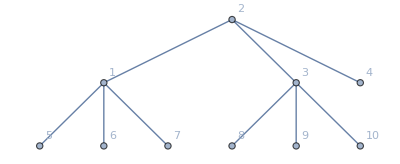

```mathematica
mgraph=MoleculeGraph[Molecule["acetone"],VertexLabels->"Name"]
```

```mathematica
mgraph//InputForm
```

Graph[{1, 2, 3, 4, 5, 6, 7, 8, 9, 10}, {UndirectedEdge[1, 2], UndirectedEdge[2, 3], 
  UndirectedEdge[2, 4], UndirectedEdge[1, 5], UndirectedEdge[1, 6], UndirectedEdge[1, 7], 
  UndirectedEdge[3, 8], UndirectedEdge[3, 9], UndirectedEdge[3, 10]}, 
 {Properties -> {6 -> {"AtomicNumber" -> 1}, UndirectedEdge[3, 10] -> {"BondOrder" -> "Single"}, 
    1 -> {"AtomicNumber" -> 6}, 2 -> {"AtomicNumber" -> 6}, UndirectedEdge[2, 4] -> 
     {"BondOrder" -> "Double"}, 10 -> {"AtomicNumber" -> 1}, 5 -> {"AtomicNumber" -> 1}, 
    UndirectedEdge[2, 3] -> {"BondOrder" -> "Single"}, 8 -> {"AtomicNumber" -> 1}, 
    3 -> {"AtomicNumber" -> 6}, 4 -> {"AtomicNumber" -> 8}, UndirectedEdge[1, 6] -> 
     {"BondOrder" -> "Single"}, 9 -> {"AtomicNumber" -> 1}, UndirectedEdge[1, 2] -> 
     {"BondOrder" -> "Single"}, UndirectedEdge[1, 7] -> {"BondOrder" -> "Single"}, 
    UndirectedEdge[1, 5] -> {"BondOrder" -> "Single"}, UndirectedEdge[3, 8] -> 
     {"BondOrder" -> "Single"}, 7 -> {"AtomicNumber" -> 1}, UndirectedEdge[3, 9] -> 
     {"BondOrder" -> "Single"}}, VertexLabels -> {"Name"}}]

```mathematica
Molecule[mgraph]
```

Molecule[…]

#### Give atom list and bond list to molecule

```mathematica
m2 = Molecule[{"N","C","Br","Cl","C"},{Bond[{1,2},"Single"],Bond[{2,3},"Single"],Bond[{2,4},"Single"],Bond[{2,5},"Single"]},StereochemistryElements->{<|"StereoType"->"Tetrahedral","ChiralCenter"->2,"Direction"->"Clockwise","FiducialAtom"->1,"Ligands"->{3,4,5}|>}]
```

#### Graph to molecule

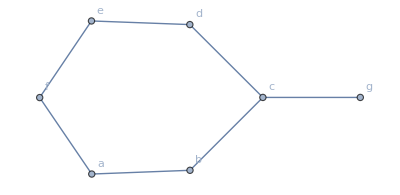

```mathematica
moleculeTest=Graph[{a<->b,b<->c,c<->d,d<->e,e<->f,f<->a,c<->g},VertexLabels->Automatic]
```

How to find a molecule from its assocation matrix?

## Limbo

### viz

```mathematica
testFun[_,x_,y__]:=List[y]
```

```mathematica
testFun[1,2,3,4]
```

{3,4}

```mathematica
(*listPointsDistance[p_List]:=EuclideanDistance[#[[1]],#[[2]]]&/@Partition[p,2,1]*)
```

```mathematica
(*lineDistance[line_Line]:=listPointsDistance[#]&/@First[line]*)
```

```mathematica
separateLineSegments[line_]:=Map[Line,First[line]]
```

```mathematica
(*
Clear[visualizeLongLineDetect]


visualizeLongLineDetect[image_Image,tVals_List,dVals_List,lCutoff_?NumericQ]:=


;

visualizeLongLineDetect[image_Image,tVal_?NumericQ,dVal_?NumericQ,lCutoff_?NumericQ]:=
Block[{lines,longLines},
lines=ImageLines[ColorNegate[image],tVal,dVal,Method->{"Segmented"->True}];
longLines=Select[Flatten@flattenLines@lines,lineDistance[#]>=lCutoff&];
HighlightImage[image,{RandomColor[],#}&/@longLines]
]

*)
(*
(*
TODO
	but don't spend so much time on visualization.
*)
visualizeLongLineDetect[image_Image,tVal_,dVal_,lCutoff_]/;Count[{tVal,dVal,lCutoff},_List]≤2:=
Table[

]*)
```

two or fewer of these three are lists

A=tVal is list
B=dVal is list
C=lCutoff is List

I want A or B or C or (A and B) or (A and C) or (B and C)...

Count  _List.

### Debugging Line

Why are they not showing up as line segments?

```mathematica
EdgeDetect[images[[10]]]
```

-Graphics-

```mathematica
Radon[images[[10]]]
```

-Graphics-

```mathematica
Radon@EdgeDetect[images[[10]]]
```

-Graphics-

```mathematica
Binarize[Radon@EdgeDetect[images[[10]]],0.02]
```

-Graphics-

Let’s see if I can find the lines with a slope near zero. Here is when I wrote the function lineSlopes.

```mathematica
First[l[[1]]]
```

{{{0.,107.001},{10.5,107.001}},{{15.,107.001},{88.,107.001}},{{92.5,107.001},{104.,107.001}},{{109.5,107.001},{125.5,107.001}},{{131.,107.001},{457.,107.001}}}

Now it works:

```mathematica
lineSlope[l[[1]]]
```

{{0.},{0.},{0.},{8.88178×10^-16},{4.35916×10^-17}}

Why are they grouped in pairs of points but not sharing corners?
Answer: Those lines are not joined.

```mathematica
HighlightImage[images[[10]],Line[{{0,100},{100,200},{300,200}}]]
```

-Graphics-

```mathematica
HighlightImage[images[[10]],Line[{{{0,100},{100,200}},{{300,200},{300,100},{250,100}}}]]
```

-Graphics-

Does it work better on the edge detected image?

```mathematica
ImageLines[EdgeDetect[images[[10]]],0.5,0.05,Method->{"Segmented"->True}]
```

{}

### Functions

```mathematica
Union[Flatten[step3[[1,1,1]]]]
```

{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{10.3484,131.064},{41.3937,110.029}}],Line[{{22.177,121.098},{52.9533,106.647}}]}

```mathematica
Flatten[step3[[1,1,1]],1]
```

{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{10.3484,131.064},{41.3937,110.029}}],Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{22.177,121.098},{52.9533,106.647}}],Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{10.3484,131.064},{41.3937,110.029}}],Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{22.177,121.098},{52.9533,106.647}}]}

```mathematica
Union[Flatten[step3[[1,1,1]],1]]
```

{Line[{{1.28498,134.888},{60.8224,99.0332}}],Line[{{1.32178,133.75},{61.6832,101.366}}],Line[{{10.3484,131.064},{41.3937,110.029}}],Line[{{22.177,121.098},{52.9533,106.647}}]}